```mathematica
Subscript[θ̃, 1]=∫∫(1/ρ1)ⅆsⅆs
```

s^2/(2 ρ1)

```mathematica
Subscript[θ, 1]=∫(1/ρ1)ⅆs
```

s/ρ1

```mathematica
β1=(s^2/Subscript[β, 0])+Subscript[β, 0]
```

s^2/β_0+β_0

```mathematica
α1=-s/Subscript[β, 0]
```

-s/β_0

```mathematica
γ1=Subscript[γ, 0]
```

γ_0

```mathematica
η1=Subscript[η, 0]+Subscript[θ̃, 1]
```

s^2/(2 ρ1)+η_0

```mathematica
ηta1=Subscript[θ, 1]
```

s/ρ1

```mathematica
h1=FullSimplify[(β1(ηta1)^2+2α1 η1 ηta1+γ1(η1)^2)/.Subscript[γ, 0]->1/Subscript[β, 0]]
```

(4 s^2 β_0^2+(s^2-2 ρ1 η_0)^2)/(4 ρ1^2 β_0)

```mathematica
ρ2=FullSimplify[((-Ld+L1 r+s-r s) ρ1)/(L1-Ld)]
```

```mathematica
/.s->Ld
```

```mathematica
FullSimplify[FullSimplify[((-Ld+L1 r+s-r s) ρ1)/(L1-Ld)/.s->s+L1]]
```

```mathematica
(-(-Ld+s-r s) ρ1)/Ld/.s->0
```

ρ1

```mathematica
/.Ld->L1(1+1/λ)
```

```mathematica
FullSimplify[∫_L1^Ld (1/ρ2)ⅆs/.r->1/ρ,L1>0,λ>0,ρ>0,ρ<1,ρ1>0]
```

FullSimplify::nonopt: Options expected (instead of ρ1 > 0) beyond position 2 in FullSimplify[ConditionalExpression[(-L1 + Ld)\ (-Log[Times[« 2 »] + Ld] + Log[Times[« 2 »] + Ld/ρ])/(-1 + 1/ρ)\ ρ1, (1/1 + Times[« 2 »] ∉ Reals || Re[1/Plus[« 2 »]] < 0 || ((Re[« 1 »] ≥ 1 || Re[« 1 »] ≤ 0) && (Power[« 2 »] ∉ Reals || Re[« 1 »] < -1))) && ((Im[« 1 »] + Times[« 2 »] + Times[« 2 »] ≥ Im[« 1 »] + Times[« 2 »] + Times[« 2 »] && (Im[« 1 »] ≥ Im[« 1 »] || Times[« 2 »] ≤ 0 || Plus[« 2 »] ≤ Plus[« 2 »])) || (Im[« 1 »] + Times[« 2 »] + Times[« 2 »] ≤ Im[« 1 »] + Times[« 2 »] + Times[« 2 »] && (Times[« 2 »] ≥ 0 || Plus[« 2 »] ≥ Plus[« 2 »] || Im[« 1 »] ≤ Im[« 1 »])))], L1 > 0, λ > 0, ρ > 0, ρ < 1, ρ1 > 0]. An option must be a rule or a list of rules.

FullSimplify[ConditionalExpression[((-L1+Ld) (-Log[-L1+Ld]+Log[(-L1+Ld)/ρ]))/((-1+1/ρ) ρ1),(1/(1-1/ρ)∉Reals||Re[1/(1-1/ρ)]<0||((Re[1/(1-1/ρ)]≥1||Re[1/(1-1/ρ)]≤0)&&(1/(-1+1/ρ)∉Reals||Re[1/(-1+1/ρ)]<-1)))&&((Im[Ld]+Im[1/ρ] Re[L1]+Im[L1] Re[1/ρ]≥Im[L1]+Im[1/ρ] Re[Ld]+Im[Ld] Re[1/ρ]&&(Im[L1]≥Im[Ld]||Im[1/ρ] (Im[L1]^2-2 Im[L1] Im[Ld]+Im[Ld]^2+(Re[L1]-Re[Ld])^2)≤0||Im[1/ρ] Re[L1]+Im[L1] Re[1/ρ]≤Im[1/ρ] Re[Ld]+Im[Ld] Re[1/ρ]))||(Im[Ld]+Im[1/ρ] Re[L1]+Im[L1] Re[1/ρ]≤Im[L1]+Im[1/ρ] Re[Ld]+Im[Ld] Re[1/ρ]&&(Im[1/ρ] (Im[L1]^2-2 Im[L1] Im[Ld]+Im[Ld]^2+(Re[L1]-Re[Ld])^2)≥0||Im[1/ρ] Re[L1]+Im[L1] Re[1/ρ]≥Im[1/ρ] Re[Ld]+Im[Ld] Re[1/ρ]||Im[L1]≤Im[Ld])))],L1>0,λ>0,ρ>0,ρ<1,ρ1>0]

```mathematica
Subscript[th, L1]=Subscript[θ, 1]/.s->L1
```

L1/ρ1

```mathematica
Subscript[tt, L1]=Subscript[θ̃, 1]/.s->L1
```

L1^2/(2 ρ1)

```mathematica
Subscript[β, L1]=Subscript[β, 0]+L1^2/Subscript[β, 0]
```

L1^2/β_0+β_0

```mathematica
Subscript[α, L1]=-L1/Subscript[β, 0]
```

-L1/β_0

```mathematica
Subscript[η, L1]=Subscript[η, 0]+Subscript[tt, L1]
```

L1^2/(2 ρ1)+η_0

```mathematica
Subscript[ηta, L1]=Subscript[th, L1]
```

L1/ρ1

```mathematica
FullSimplify[FullSimplify[(-(-Ld+L1+s-r s) ρ1)/(Ld-L1)]/.r->1/ρ/.Ld->L1+L2/.s->L2]
```

4.111+16.2831 L2

```mathematica
ρ2=FullSimplify[FullSimplify[(-(-Ld+L1+s-r s) ρ1)/(Ld-L1)]/.r->1/ρ/.L1->Ld/(1+1/λ)]
```

((-s (1+λ) (-1+ρ)+Ld ρ) ρ1)/(Ld ρ)

```mathematica
Solve[((Ld+s (1+λ) (-1+1/ρ)) ρ1)/Ld==rho2,Ld]
```

{{Ld→(s (1+λ) (-1+ρ) ρ1)/(ρ (-rho2+ρ1))}}

```mathematica
Subscript[θ, 2]=Simplify[∫_L1^s (1/ρ2)ⅆs,{r>0,r>1,λ>0,ρ1>0,L1<s,L1>0,Ld>0,L1<Ld}]
```

```mathematica
Subscript[θ̃, 2]=Simplify[∫_L1^s (Subscript[θ, 2])ⅆs,{r>0,r>1,λ>0,ρ1>0,L1>0,L1<s,Ld>0,L1<Ld}]
```

```mathematica
FullSimplify[-((L1-Ld) ((-1+r) (L1-s)+(-Ld+L1 r+s-r s) Log[-L1+Ld]+(Ld-L1 r+(-1+r) s) Log[Ld-L1 r+(-1+r) s]))/((-1+r)^2 ρ1)/.r->1/ρ]
```

((L1-Ld) ρ ((L1-s) (-1+ρ)-(L1+s (-1+ρ)-Ld ρ) (Log[-L1+Ld]-Log[Ld-s+(-L1+s)/ρ])))/((-1+ρ)^2 ρ1)

```mathematica
FullSimplify[∫∫(1/ρ2)ⅆsⅆs]
```

```mathematica
FullSimplify[(Ld ρ (Ld ρ Log[s (1+λ) (-1+ρ)-Ld ρ]-s (1+λ) (-1+ρ) (-1+Log[-s (1+λ) (-1+ρ)+Ld ρ])))/((1+λ)^2 (-1+ρ)^2 ρ1)/.(-s (1+λ) (-1+ρ)+Ld ρ)->rho2 Ld ρ/ρ1/.(s (1+λ) (-1+ρ)-Ld ρ)->-rho2 Ld ρ/ρ1]
```

(Ld ρ (Ld ρ Log[-(Ld rho2 ρ)/ρ1]-s (1+λ) (-1+ρ) (-1+Log[(Ld rho2 ρ)/ρ1])))/((1+λ)^2 (-1+ρ)^2 ρ1)

```mathematica
FullSimplify[∫(1/ρ2)ⅆs]
```

-(Ld ρ Log[-s (1+λ) (-1+ρ)+Ld ρ])/((1+λ) (-1+ρ) ρ1)

```mathematica
β2=Subscript[β, L1]-2(s-L1)Subscript[α, L1]+(s-L1)^2 Subscript[γ, 0]
```

L1^2/β_0+(2 L1 (-L1+s))/β_0+β_0+(-L1+s)^2 γ_0

```mathematica
α2=Subscript[α, L1]-(s-L1) Subscript[γ, 0]
```

-L1/β_0-(-L1+s) γ_0

```mathematica
γ2=Subscript[γ, 0]
```

γ_0

```mathematica
η2=Subscript[η, L1]+(s-L1) Subscript[ηta, L1]+Subscript[θ̃, 2]
```

L1^2/(2 ρ1)+(L1 (-L1+s))/ρ1-((L1-Ld) ((-1+r) (L1-s)+(-Ld+L1 r+s-r s) Log[-L1+Ld]+(Ld-L1 r+(-1+r) s) Log[Ld-L1 r+(-1+r) s]))/((-1+r)^2 ρ1)+η_0

```mathematica
ηta2=Subscript[θ, 2]+ Subscript[ηta, L1]
```

L1/ρ1+((L1-Ld) (Log[-L1+Ld]-Log[Ld-L1 r+(-1+r) s]))/((-1+r) ρ1)

```mathematica
h2=FullSimplify[(β2(ηta2)^2+2α2 η2 ηta2+γ2(η2)^2)/.Subscript[γ, 0]->1/Subscript[β, 0]]
```

1/(4 (-1+r)^4 ρ1^2 β_0)(4 (-1+r)^2 (L1 (-1+r)+(L1-Ld) (Log[-L1+Ld]-Log[Ld-L1 r+(-1+r) s]))^2 β_0^2+((-1+r) (L1^2 (1+r)+2 Ld s-2 L1 (Ld+s))+2 (L1-Ld) (-Ld+L1 r) (Log[-L1+Ld]-Log[Ld-L1 r+(-1+r) s])-2 (-1+r)^2 ρ1 η_0)^2)

edw vriskw tin oliki emittance prosthetontas ta duo kommatia, me tin voitheia twn dispersion invariants h1 kai h2 , wste na tin kanw minimize kai meta na vrw ta η_0 , β_0 gia tin TME, gia olo to dipolo opou ∫_0^L1 -> 2∫_0^L1  kai opou ∫_L1^Ld -> 2∫_L1^Ld . to Ld einai to miso mikos dipolou.

```mathematica
e=FullSimplify[C((2/(2L1)∫_0^L1 h1/ρ1^3 ⅆs)+(2/(2(Ld-L1))∫_L1^Ld h2/ρ2^3 ⅆs))/(G1+G2)/.G1->(2/(2L1)∫_0^L1 1/ρ1^2 ⅆs)/.G2->(2/(2(Ld-L1))∫_L1^Ld 1/ρ2^2 ⅆs)/.Ld->L1(1+1/λ),{r>0,r>1,λ>0,ρ1>0,L1<s,L1>0,Ld>0,L1<Ld}]
```

1/(120 (-1+r)^5 r (1+r) λ^4 ρ1^3 β_0)C (3 L1^4 (-10 (-1+r) (-5+11 r)+40 (-1+r)^3 λ+20 (-1+r)^4 λ^2+10 (-1+r)^4 (1+r) λ^3+(-1+r)^5 (5+r (5+2 r)) λ^4+20 Log[r] (-3+4 r+2 r^2-4 (-1+r)^2 λ-(-1+r)^3 λ^3-(1+λ-r λ)^2 Log[r]))+10 (-1+r)^2 λ^2 (L1^2 (3 (-1+r^2)+6 (-1+r)^2 (1+r) λ+2 (-1+r)^3 (3+r (3+2 r)) λ^2-6 Log[r] (1+2 (-1+r) λ+Log[r])) β_0^2+2 ρ1 η_0 (L1^2 ((-1+r) (9-3 r-3 (-1+r^2) λ-(-1+r)^2 (3+r (3+2 r)) λ^2)+6 (-1+(-1+r) λ) Log[r])+3 (-1+r)^3 (1+r+2 r^2) λ^2 ρ1 η_0)))

```mathematica
Simplify[Solve[{D[e, Subscript[η, 0]]==0,D[e, Subscript[β, 0]]==0},{Subscript[β, 0],Subscript[η, 0]}],{r>0,r>1,λ>0,ρ1>0,L1>0,(-((-1+r)^3 (1+r+2 r^2) λ^2 ((-1+r) (3-6 λ-2 r^2 (-3+λ) λ+6 λ^2-2 r^3 λ^2+4 r^4 λ^2+r (3-6 λ^2))-6 (1+2 (-1+r) λ) Log[r]-6 Log[r]^2))/((-1+r)^2 (-16 r^7 λ^4+16 r^8 λ^4-270 r (1+λ)+45 (1+λ)^2-24 r^6 λ^3 (-5+2 λ)+4 r^5 λ^2 (75-60 λ+8 λ^2)+r^4 λ (720-735 λ+112 λ^3)+3 r^2 (-45+210 λ-90 λ^2-40 λ^3+16 λ^4)-6 r^3 (330+195 λ-110 λ^2-40 λ^3+24 λ^4))-120 (-1+r) r^2 (2 r^3 λ^3+λ (6+λ-2 λ^2)+r^2 (-6+12 λ+λ^2-6 λ^3)+r (-15-18 λ-2 λ^2+6 λ^3)) Log[r]-180 r^2 (-1+2 r) (-1+(-1+r) λ)^2 Log[r]^2))<0,Subscript[β, 0]>0,Subscript[β, 0]∈Reals,(ⅈ L1)/(√30 √(-((-1+r)^3 (1+r+2 r^2) λ^2 (3 (-1+r^2)+6 (-1+r)^2 (1+r) λ+2 (-1+r)^3 (3+r (3+2 r)) λ^2-6 Log[r] (1+2 (-1+r) λ+Log[r])))/((-1+r)^2 (-45 (-1+r (6+r (3+44 r)))+90 (-1+r) (-1+r (2+r (-5+8 r))) λ+15 (-1+r)^2 (3+r (6+r (-9+20 r))) λ^2+120 (-1+r)^3 r^2 (1+r) λ^3+16 (-1+r)^4 r^2 (3+r (3+r)) λ^4)+60 r^2 Log[r] (2 (-1+r) (3 r (5+2 r)-6 (-1+r) (-1+2 r) λ-(-1+r)^2 λ^2-2 (-1+r)^3 λ^3)-3 (-1+2 r) (1+λ-r λ)^2 Log[r]))))∈Reals,r>0,r>1,λ>0,ρ1>0,L1>0}]
```

{{β_0→-(ⅈ L1)/(√30 √(-((-1+r)^3 (1+r+2 r^2) λ^2 ((-1+r) (3-6 λ-2 r^2 (-3+λ) λ+6 λ^2-2 r^3 λ^2+4 r^4 λ^2+r (3-6 λ^2))-6 (1+2 (-1+r) λ) Log[r]-6 Log[r]^2))/((-1+r)^2 (-16 r^7 λ^4+16 r^8 λ^4-270 r (1+λ)+45 (1+λ)^2-24 r^6 λ^3 (-5+2 λ)+4 r^5 λ^2 (75-60 λ+8 λ^2)+r^4 λ (720-735 λ+112 λ^3)+3 r^2 (-45+210 λ-90 λ^2-40 λ^3+16 λ^4)-6 r^3 (330+195 λ-110 λ^2-40 λ^3+24 λ^4))-120 (-1+r) r^2 (2 r^3 λ^3+λ (6+λ-2 λ^2)+r^2 (-6+12 λ+λ^2-6 λ^3)+r (-15-18 λ-2 λ^2+6 λ^3)) Log[r]-180 r^2 (-1+2 r) (-1+(-1+r) λ)^2 Log[r]^2))),η_0→(L1^2 ((-1+r) (-r^2 (-3+λ) λ-r^3 λ^2+2 r^4 λ^2-3 r (-1+λ^2)+3 (-3-λ+λ^2))+(6-6 (-1+r) λ) Log[r]))/(6 (-1+r)^3 (1+r+2 r^2) λ^2 ρ1)},{β_0→(ⅈ L1)/(√30 √(-((-1+r)^3 (1+r+2 r^2) λ^2 ((-1+r) (3-6 λ-2 r^2 (-3+λ) λ+6 λ^2-2 r^3 λ^2+4 r^4 λ^2+r (3-6 λ^2))-6 (1+2 (-1+r) λ) Log[r]-6 Log[r]^2))/((-1+r)^2 (-16 r^7 λ^4+16 r^8 λ^4-270 r (1+λ)+45 (1+λ)^2-24 r^6 λ^3 (-5+2 λ)+4 r^5 λ^2 (75-60 λ+8 λ^2)+r^4 λ (720-735 λ+112 λ^3)+3 r^2 (-45+210 λ-90 λ^2-40 λ^3+16 λ^4)-6 r^3 (330+195 λ-110 λ^2-40 λ^3+24 λ^4))-120 (-1+r) r^2 (2 r^3 λ^3+λ (6+λ-2 λ^2)+r^2 (-6+12 λ+λ^2-6 λ^3)+r (-15-18 λ-2 λ^2+6 λ^3)) Log[r]-180 r^2 (-1+2 r) (-1+(-1+r) λ)^2 Log[r]^2))),η_0→(L1^2 ((-1+r) (-r^2 (-3+λ) λ-r^3 λ^2+2 r^4 λ^2-3 r (-1+λ^2)+3 (-3-λ+λ^2))+(6-6 (-1+r) λ) Log[r]))/(6 (-1+r)^3 (1+r+2 r^2) λ^2 ρ1)}}

```mathematica
-((-1+r)^3 (1+r+2 r^2) λ^2 (3 (-1+r^2)+6 (-1+r)^2 (1+r) λ+2 (-1+r)^3 (3+r (3+2 r)) λ^2-6 Log[r] (1+2 (-1+r) λ+Log[r])))/((-1+r)^2 (-45 (-1+r (6+r (3+44 r)))+90 (-1+r) (-1+r (2+r (-5+8 r))) λ+15 (-1+r)^2 (3+r (6+r (-9+20 r))) λ^2+120 (-1+r)^3 r^2 (1+r) λ^3+16 (-1+r)^4 r^2 (3+r (3+r)) λ^4)+60 r^2 Log[r] (2 (-1+r) (3 r (5+2 r)-6 (-1+r) (-1+2 r) λ-(-1+r)^2 λ^2-2 (-1+r)^3 λ^3)-3 (-1+2 r) (1+λ-r λ)^2 Log[r]))/.λ->0.2/.r->2
```

-0.0151063

```mathematica
{beta,eta}=Simplify[{L1/(√30 √(((-1+r)^3 (1+r+2 r^2) λ^2 ((-1+r) (3-6 λ-2 r^2 (-3+λ) λ+6 λ^2-2 r^3 λ^2+4 r^4 λ^2+r (3-6 λ^2))-6 (1+2 (-1+r) λ) Log[r]-6 Log[r]^2))/((-1+r)^2 (-16 r^7 λ^4+16 r^8 λ^4-270 r (1+λ)+45 (1+λ)^2-24 r^6 λ^3 (-5+2 λ)+4 r^5 λ^2 (75-60 λ+8 λ^2)+r^4 λ (720-735 λ+112 λ^3)+3 r^2 (-45+210 λ-90 λ^2-40 λ^3+16 λ^4)-6 r^3 (330+195 λ-110 λ^2-40 λ^3+24 λ^4))-120 (-1+r) r^2 (2 r^3 λ^3+λ (6+λ-2 λ^2)+r^2 (-6+12 λ+λ^2-6 λ^3)+r (-15-18 λ-2 λ^2+6 λ^3)) Log[r]-180 r^2 (-1+2 r) (-1+(-1+r) λ)^2 Log[r]^2))),(L1^2 ((-1+r) (-r^2 (-3+λ) λ-r^3 λ^2+2 r^4 λ^2-3 r (-1+λ^2)+3 (-3-λ+λ^2))+(6-6 (-1+r) λ) Log[r]))/(6 (-1+r)^3 (1+r+2 r^2) λ^2 ρ1)}/.r->1/ρ]
```

{L1/(√30 √((λ^2 (-1+ρ)^3 (2+ρ+ρ^2) ((-1+ρ) (3 ρ^3 (1+ρ)-6 λ ρ^2 (-1+ρ^2)+2 λ^2 (-1+ρ)^2 (2+3 ρ+3 ρ^2))+6 ρ^4 (-2 λ (-1+ρ)+ρ) Log[1/ρ]+6 ρ^5 Log[1/ρ]^2))/((-1+ρ)^2 (-120 λ^3 (-1+ρ)^3 ρ^2 (1+ρ)+16 λ^4 (-1+ρ)^4 (1+3 ρ+3 ρ^2)+45 ρ^5 (-44-3 ρ-6 ρ^2+ρ^3)+15 λ^2 (-1+ρ)^2 ρ^3 (20-9 ρ+6 ρ^2+3 ρ^3)+90 λ ρ^4 (8-13 ρ+7 ρ^2-3 ρ^3+ρ^4))-120 (-1+ρ) ρ^4 (2 λ^3 (-1+ρ)^3-λ^2 (-1+ρ)^2 ρ+3 ρ (2+5 ρ)-6 λ ρ (2-3 ρ+ρ^2)) Log[1/ρ]+180 (-2+ρ) ρ^5 (λ (-1+ρ)+ρ)^2 Log[1/ρ]^2))),(L1^2 ((-1+ρ) (3 (1-3 ρ) ρ^3-3 λ ρ^2 (-1+ρ^2)+λ^2 (-1+ρ)^2 (2+3 ρ+3 ρ^2))-6 ρ^4 (λ (-1+ρ)+ρ) Log[1/ρ]))/(6 λ^2 (-1+ρ)^3 (2+ρ+ρ^2) ρ1)}

ta H1 kai H2 parakatw einai ta dispersion invariants kanontas tin antikatastasi twn η_0 , β_0 gia tin TME, vevaiws gia β_0 thetiko.

```mathematica
H1=Simplify[Simplify[(β1(ηta1)^2+2α1 η1 ηta1+γ1(η1)^2)/.Subscript[γ, 0]->1/Subscript[β, 0]]/.{Subscript[β, 0]->beta,Subscript[η, 0]->eta}]
```

1/(2 L1 ρ1^2)√(15/2) √((λ^2 (-1+ρ)^3 (2+ρ+ρ^2) ((-1+ρ) (3 ρ^3 (1+ρ)-6 λ ρ^2 (-1+ρ^2)+2 λ^2 (-1+ρ)^2 (2+3 ρ+3 ρ^2))+6 ρ^4 (-2 λ (-1+ρ)+ρ) Log[1/ρ]+6 ρ^5 Log[1/ρ]^2))/((-1+ρ)^2 (-120 λ^3 (-1+ρ)^3 ρ^2 (1+ρ)+16 λ^4 (-1+ρ)^4 (1+3 ρ+3 ρ^2)+45 ρ^5 (-44-3 ρ-6 ρ^2+ρ^3)+15 λ^2 (-1+ρ)^2 ρ^3 (20-9 ρ+6 ρ^2+3 ρ^3)+90 λ ρ^4 (8-13 ρ+7 ρ^2-3 ρ^3+ρ^4))-120 (-1+ρ) ρ^4 (2 λ^3 (-1+ρ)^3-λ^2 (-1+ρ)^2 ρ+3 ρ (2+5 ρ)-6 λ ρ (2-3 ρ+ρ^2)) Log[1/ρ]+180 (-2+ρ) ρ^5 (λ (-1+ρ)+ρ)^2 Log[1/ρ]^2)) ((2 L1^2 s^2 ((-1+ρ)^2 (-120 λ^3 (-1+ρ)^3 ρ^2 (1+ρ)+16 λ^4 (-1+ρ)^4 (1+3 ρ+3 ρ^2)+45 ρ^5 (-44-3 ρ-6 ρ^2+ρ^3)+15 λ^2 (-1+ρ)^2 ρ^3 (20-9 ρ+6 ρ^2+3 ρ^3)+90 λ ρ^4 (8-13 ρ+7 ρ^2-3 ρ^3+ρ^4))-120 (-1+ρ) ρ^4 (2 λ^3 (-1+ρ)^3-λ^2 (-1+ρ)^2 ρ+3 ρ (2+5 ρ)-6 λ ρ (2-3 ρ+ρ^2)) Log[1/ρ]+180 (-2+ρ) ρ^5 (λ (-1+ρ)+ρ)^2 Log[1/ρ]^2))/(15 λ^2 (-1+ρ)^3 (2+ρ+ρ^2) ((-1+ρ) (3 ρ^3 (1+ρ)-6 λ ρ^2 (-1+ρ^2)+2 λ^2 (-1+ρ)^2 (2+3 ρ+3 ρ^2))+6 ρ^4 (-2 λ (-1+ρ)+ρ) Log[1/ρ]+6 ρ^5 Log[1/ρ]^2))+(s^2-(L1^2 ((-1+ρ) (3 (1-3 ρ) ρ^3-3 λ ρ^2 (-1+ρ^2)+λ^2 (-1+ρ)^2 (2+3 ρ+3 ρ^2))-6 ρ^4 (λ (-1+ρ)+ρ) Log[1/ρ]))/(3 λ^2 (-1+ρ)^3 (2+ρ+ρ^2)))^2)

```mathematica
H2=Simplify[Simplify[(β2(ηta2)^2+2α2 η2 ηta2+γ2(η2)^2)/.Subscript[γ, 0]->1/Subscript[β, 0]/.r->1/ρ]/.{Subscript[β, 0]->beta,Subscript[η, 0]->eta}]
```

1/(6 L1 ρ1^2)√(5/6) √((λ^2 (-1+ρ)^3 (2+ρ+ρ^2) ((-1+ρ) (3 ρ^3 (1+ρ)-6 λ ρ^2 (-1+ρ^2)+2 λ^2 (-1+ρ)^2 (2+3 ρ+3 ρ^2))+6 ρ^4 (-2 λ (-1+ρ)+ρ) Log[1/ρ]+6 ρ^5 Log[1/ρ]^2))/((-1+ρ)^2 (-120 λ^3 (-1+ρ)^3 ρ^2 (1+ρ)+16 λ^4 (-1+ρ)^4 (1+3 ρ+3 ρ^2)+45 ρ^5 (-44-3 ρ-6 ρ^2+ρ^3)+15 λ^2 (-1+ρ)^2 ρ^3 (20-9 ρ+6 ρ^2+3 ρ^3)+90 λ ρ^4 (8-13 ρ+7 ρ^2-3 ρ^3+ρ^4))-120 (-1+ρ) ρ^4 (2 λ^3 (-1+ρ)^3-λ^2 (-1+ρ)^2 ρ+3 ρ (2+5 ρ)-6 λ ρ (2-3 ρ+ρ^2)) Log[1/ρ]+180 (-2+ρ) ρ^5 (λ (-1+ρ)+ρ)^2 Log[1/ρ]^2)) (1/(-1+ρ)^236 (s^2+(L1^2 ((-1+ρ)^2 (-120 λ^3 (-1+ρ)^3 ρ^2 (1+ρ)+16 λ^4 (-1+ρ)^4 (1+3 ρ+3 ρ^2)+45 ρ^5 (-44-3 ρ-6 ρ^2+ρ^3)+15 λ^2 (-1+ρ)^2 ρ^3 (20-9 ρ+6 ρ^2+3 ρ^3)+90 λ ρ^4 (8-13 ρ+7 ρ^2-3 ρ^3+ρ^4))-120 (-1+ρ) ρ^4 (2 λ^3 (-1+ρ)^3-λ^2 (-1+ρ)^2 ρ+3 ρ (2+5 ρ)-6 λ ρ (2-3 ρ+ρ^2)) Log[1/ρ]+180 (-2+ρ) ρ^5 (λ (-1+ρ)+ρ)^2 Log[1/ρ]^2))/(30 λ^2 (-1+ρ)^3 (2+ρ+ρ^2) ((-1+ρ) (3 ρ^3 (1+ρ)-6 λ ρ^2 (-1+ρ^2)+2 λ^2 (-1+ρ)^2 (2+3 ρ+3 ρ^2))+6 ρ^4 (-2 λ (-1+ρ)+ρ) Log[1/ρ]+6 ρ^5 Log[1/ρ]^2))) (L1-L1 ρ+(L1-Ld) ρ Log[-L1+Ld]+(-L1+Ld) ρ Log[(-L1+s+Ld ρ-s ρ)/ρ])^2-12 s (L1-((L1-Ld) ρ (Log[-L1+Ld]-Log[(-L1+s+Ld ρ-s ρ)/ρ]))/(-1+ρ)) (3 L1^2+6 L1 (-L1+s)+(L1^2 ((-1+ρ) (3 (1-3 ρ) ρ^3-3 λ ρ^2 (-1+ρ^2)+λ^2 (-1+ρ)^2 (2+3 ρ+3 ρ^2))-6 ρ^4 (λ (-1+ρ)+ρ) Log[1/ρ]))/(λ^2 (-1+ρ)^3 (2+ρ+ρ^2))+(6 (L1-Ld) ρ ((L1-s) (-1+ρ)+(-L1+s+Ld ρ-s ρ) Log[-L1+Ld]+(L1+s (-1+ρ)-Ld ρ) Log[(-L1+s+Ld ρ-s ρ)/ρ]))/(-1+ρ)^2)+(3 L1^2+6 L1 (-L1+s)+(L1^2 ((-1+ρ) (3 (1-3 ρ) ρ^3-3 λ ρ^2 (-1+ρ^2)+λ^2 (-1+ρ)^2 (2+3 ρ+3 ρ^2))-6 ρ^4 (λ (-1+ρ)+ρ) Log[1/ρ]))/(λ^2 (-1+ρ)^3 (2+ρ+ρ^2))+(6 (L1-Ld) ρ ((L1-s) (-1+ρ)+(-L1+s+Ld ρ-s ρ) Log[-L1+Ld]+(L1+s (-1+ρ)-Ld ρ) Log[(-L1+s+Ld ρ-s ρ)/ρ]))/(-1+ρ)^2)^2)

kanw ta parakatw plots gia tuxaies times ρ, λ wste na dw tin ekseliksi tou total dispersion invariant

```mathematica
(2 L1 (λ (-1+ρ)+ρ Log[ρ]))/(λ (-1+ρ) ρ1)/.L1->Ld/(1+1/λ)/.Ld->0.5/.ρ->0.2/.λ->0.2/.ρ1->5.4
```

0.0929567

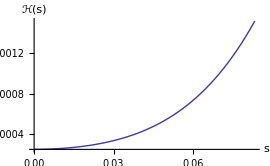

```mathematica
ph1=Plot[H1/.L1->Ld/(1+1/λ)/.Ld->0.5/.ρ->0.2/.λ->0.2/.ρ1->5.4,{s,0,Ld/(1+1/λ)/.Ld->0.5/.λ->0.2},PlotRange->All,AxesLabel->{"s","ℋ(s)"},LabelStyle->Directive[20]]
```

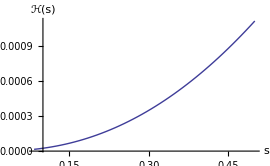

```mathematica
ph2=Plot[H2/.L1->Ld/(1+1/λ)/.Ld->0.5/.ρ->0.2/.λ->0.2/.ρ1->5.4,{s,(Ld/(1+1/λ)/.Ld->0.5/.λ->0.2),0.5},PlotRange->All,AxesLabel->{"s","ℋ(s)"},LabelStyle->Directive[20]]
```

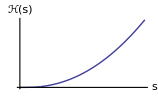

```mathematica
Show[{ph1,ph2},PlotRange->All,Ticks->None]
```

edw upologizw tin TME me antikatastasi twn  η_0 , β_0 pou vrika,  C=Cq*γ^2/J

```mathematica
emi=FullSimplify[e/.r->1/ρ/.{Subscript[β, 0]->beta,Subscript[η, 0]->eta},{λ>0}]
```

(C L1^3 (-6 λ (-1+ρ)^2 ρ^2 (1+ρ)+3 ρ^3 (-1+ρ^2)+2 λ^2 (-1+ρ)^3 (2+3 ρ (1+ρ))+6 ρ^4 Log[1/ρ] (-2 λ (-1+ρ)+ρ+ρ Log[1/ρ])))/(6 √30 λ^3 (-1+ρ)^3 (1+ρ) ρ1^3 √(((-1+ρ)^3 (2+ρ+ρ^2) (-6 λ (-1+ρ)^2 ρ^2 (1+ρ)+3 ρ^3 (-1+ρ^2)+2 λ^2 (-1+ρ)^3 (2+3 ρ (1+ρ))+6 ρ^4 Log[1/ρ] (-2 λ (-1+ρ)+ρ+ρ Log[1/ρ])))/((-1+ρ)^2 (-120 λ^3 (-1+ρ)^3 ρ^2 (1+ρ)+16 λ^4 (-1+ρ)^4 (1+3 ρ (1+ρ))+15 λ^2 (-1+ρ)^2 ρ^3 (20+3 (-1+ρ) ρ (3+ρ))+45 ρ^5 (-44+ρ (-3+(-6+ρ) ρ))+90 λ (-1+ρ) ρ^4 (-8+ρ (5+(-2+ρ) ρ)))+60 ρ^4 Log[1/ρ] (-2 (-1+ρ) (2 λ^3 (-1+ρ)^3-6 λ (-2+ρ) (-1+ρ) ρ-λ^2 (-1+ρ)^2 ρ+3 ρ (2+5 ρ))+3 (-2+ρ) ρ (λ (-1+ρ)+ρ)^2 Log[1/ρ]))))

edw upologizw tin oliki gwnia wste na ginoun aplopoiiseis, einai gia olo to mikos dipolou ara opou ∫_0^L1 -> 2∫_0^L1  kai opou ∫_L1^Ld -> 2∫_L1^Ld . to Ld einai to miso mikos dipolou.

```mathematica
thetatot=FullSimplify[2(∫_0^L1 (1/ρ1)ⅆs+∫_L1^Ld (1/ρ2)ⅆs)/.r->1/ρ/.Ld->L1(1+1/λ),{ρ>0,ρ<1,λ>0,ρ1>0,L1<s,L1>0,Ld>0,L1<Ld}]
```

(2 L1 (λ (-1+ρ)+ρ Log[ρ]))/(λ (-1+ρ) ρ1)

```mathematica
(2 L1 (λ (-1+ρ)+ρ Log[ρ]))/(λ (-1+ρ) ρ1)/2/.L1->Ld/(1+1/λ)/.ρ1->5.4/.Ld->0.58/.ρ->0.404/.λ->0.1017661679
```

0.0698132

```mathematica
FullSimplify[Solve[((2 L1 (λ (-1+ρ)+ρ Log[ρ]))/(λ (-1+ρ) ρ1)/.L1->Ld/(1+1/λ))==2π/Nd,λ]]
```

{{λ→(π (-1+ρ) ρ1-Ld Nd ρ Log[ρ])/((-1+ρ) (Ld Nd-π ρ1))}}

```mathematica
FullSimplify[∫_0^L1 ∫_0^L1 (1/ρ1)ⅆsⅆs+∫_L1^Ld ∫_L1^Ld (1/ρ2)ⅆsⅆs/.r->1/ρ/.Ld->L1(1+1/λ),{ρ>0,ρ<1,λ>0,ρ1>0,L1<s,L1>0,Ld>0,L1<Ld}]
```

(L1^2 (1+(ρ Log[ρ])/(λ^2 (-1+ρ))))/ρ1

```mathematica
FullSimplify[(∫_L1^Ld (1/ρ2)ⅆs)/.r->1/ρ/.Ld->L1(1+1/λ),{ρ>0,ρ<1,λ>0,ρ1>0,L1<s,L1>0,Ld>0,L1<Ld}]
```

(L1 ρ Log[ρ])/(λ (-1+ρ) ρ1)

```mathematica
FullSimplify[2(∫_0^L1 ∫_0^L1 (1/ρ1)ⅆsⅆs+∫_L1^Ld ∫_L1^Ld (1/ρ2)ⅆsⅆs)/.r->1/ρ/.Ld->L1(1+1/λ),{ρ>0,ρ<1,λ>0,ρ1>0,L1<s,L1>0,Ld>0,L1<Ld}]
```

(2 L1^2 (λ^2 (-1+ρ)+ρ Log[ρ]))/(λ^2 (-1+ρ) ρ1)

```mathematica
emit=Simplify[emi/.L1^3/(λ^3  ρ1^3(-1+ρ)^3)->θ^3/(2(λ (-1+ρ)+ρ Log[ρ]))^3/.C->Cq γ^2/Subscript[J, x]]
```

(Cq γ^2 θ^3 (-6 λ (-1+ρ)^2 ρ^2 (1+ρ)+3 ρ^3 (-1+ρ^2)+2 λ^2 (-1+ρ)^3 (2+3 ρ (1+ρ))+6 ρ^4 Log[1/ρ] (-2 λ (-1+ρ)+ρ+ρ Log[1/ρ])))/(48 √30 (1+ρ) √(((-1+ρ)^3 (2+ρ+ρ^2) (-6 λ (-1+ρ)^2 ρ^2 (1+ρ)+3 ρ^3 (-1+ρ^2)+2 λ^2 (-1+ρ)^3 (2+3 ρ (1+ρ))+6 ρ^4 Log[1/ρ] (-2 λ (-1+ρ)+ρ+ρ Log[1/ρ])))/((-1+ρ)^2 (-120 λ^3 (-1+ρ)^3 ρ^2 (1+ρ)+16 λ^4 (-1+ρ)^4 (1+3 ρ (1+ρ))+15 λ^2 (-1+ρ)^2 ρ^3 (20+3 (-1+ρ) ρ (3+ρ))+45 ρ^5 (-44+ρ (-3+(-6+ρ) ρ))+90 λ (-1+ρ) ρ^4 (-8+ρ (5+(-2+ρ) ρ)))+60 ρ^4 Log[1/ρ] (-2 (-1+ρ) (2 λ^3 (-1+ρ)^3-6 λ (-2+ρ) (-1+ρ) ρ-λ^2 (-1+ρ)^2 ρ+3 ρ (2+5 ρ))+3 (-2+ρ) ρ (λ (-1+ρ)+ρ)^2 Log[1/ρ]))) (λ (-1+ρ)+ρ Log[ρ])^3 J_x)

```mathematica
N[ProductLog[Log[10]]]
```

0.918761

```mathematica
fr=Simplify[(Cq γ^3 θ^3/(Subscript[J, x] √15 12))/(γ emit),{ρ>0,ρ<1,λ>0}]
```

(4 √2 (1+ρ) (λ (-1+ρ)+ρ Log[ρ])^3 √(((-1+ρ)^3 (2+ρ+ρ^2) (-6 λ (-1+ρ)^2 ρ^2 (1+ρ)+3 ρ^3 (-1+ρ^2)+2 λ^2 (-1+ρ)^3 (2+3 ρ (1+ρ))+6 ρ^4 Log[ρ] (2 λ (-1+ρ)-ρ+ρ Log[ρ])))/((-1+ρ)^2 (-120 λ^3 (-1+ρ)^3 ρ^2 (1+ρ)+16 λ^4 (-1+ρ)^4 (1+3 ρ (1+ρ))+15 λ^2 (-1+ρ)^2 ρ^3 (20+3 (-1+ρ) ρ (3+ρ))+45 ρ^5 (-44+ρ (-3+(-6+ρ) ρ))+90 λ (-1+ρ) ρ^4 (-8+ρ (5+(-2+ρ) ρ)))-60 ρ^4 Log[ρ] (-2 (-1+ρ) (2 λ^3 (-1+ρ)^3-6 λ (-2+ρ) (-1+ρ) ρ-λ^2 (-1+ρ)^2 ρ+3 ρ (2+5 ρ))-3 (-2+ρ) ρ (λ (-1+ρ)+ρ)^2 Log[ρ]))))/((-1+ρ) (3 ρ^3 (1+ρ)-6 λ ρ^2 (-1+ρ^2)+2 λ^2 (-1+ρ)^2 (2+3 ρ+3 ρ^2))+6 (2 λ (-1+ρ)-ρ) ρ^4 Log[ρ]+6 ρ^5 Log[ρ]^2)

```mathematica
frtr=(4 √2 (1+ρ) (λ (-1+ρ)+ρ Log[ρ])^3 √(((-1+ρ)^3 (2+ρ+ρ^2) (-6 λ (-1+ρ)^2 ρ^2 (1+ρ)+3 ρ^3 (-1+ρ^2)+2 λ^2 (-1+ρ)^3 (2+3 ρ (1+ρ))+6 ρ^4 Log[ρ] (2 λ (-1+ρ)-ρ+ρ Log[ρ])))/((-1+ρ)^2 (-120 λ^3 (-1+ρ)^3 ρ^2 (1+ρ)+16 λ^4 (-1+ρ)^4 (1+3 ρ (1+ρ))+15 λ^2 (-1+ρ)^2 ρ^3 (20+3 (-1+ρ) ρ (3+ρ))+45 ρ^5 (-44+ρ (-3+(-6+ρ) ρ))+90 λ (-1+ρ) ρ^4 (-8+ρ (5+(-2+ρ) ρ)))-60 ρ^4 Log[ρ] (-2 (-1+ρ) (2 λ^3 (-1+ρ)^3-6 λ (-2+ρ) (-1+ρ) ρ-λ^2 (-1+ρ)^2 ρ+3 ρ (2+5 ρ))-3 (-2+ρ) ρ (λ (-1+ρ)+ρ)^2 Log[ρ]))))/((-1+ρ) (3 ρ^3 (1+ρ)-6 λ ρ^2 (-1+ρ^2)+2 λ^2 (-1+ρ)^2 (2+3 ρ+3 ρ^2))+6 (2 λ (-1+ρ)-ρ) ρ^4 Log[ρ]+6 ρ^5 Log[ρ]^2)
```

(4 √2 (1+ρ) (λ (-1+ρ)+ρ Log[ρ])^3 √(((-1+ρ)^3 (2+ρ+ρ^2) (-6 λ (-1+ρ)^2 ρ^2 (1+ρ)+3 ρ^3 (-1+ρ^2)+2 λ^2 (-1+ρ)^3 (2+3 ρ (1+ρ))+6 ρ^4 Log[ρ] (2 λ (-1+ρ)-ρ+ρ Log[ρ])))/((-1+ρ)^2 (-120 λ^3 (-1+ρ)^3 ρ^2 (1+ρ)+16 λ^4 (-1+ρ)^4 (1+3 ρ (1+ρ))+15 λ^2 (-1+ρ)^2 ρ^3 (20+3 (-1+ρ) ρ (3+ρ))+45 ρ^5 (-44+ρ (-3+(-6+ρ) ρ))+90 λ (-1+ρ) ρ^4 (-8+ρ (5+(-2+ρ) ρ)))-60 ρ^4 Log[ρ] (-2 (-1+ρ) (2 λ^3 (-1+ρ)^3-6 λ (-2+ρ) (-1+ρ) ρ-λ^2 (-1+ρ)^2 ρ+3 ρ (2+5 ρ))-3 (-2+ρ) ρ (λ (-1+ρ)+ρ)^2 Log[ρ]))))/((-1+ρ) (3 ρ^3 (1+ρ)-6 λ ρ^2 (-1+ρ^2)+2 λ^2 (-1+ρ)^2 (2+3 ρ+3 ρ^2))+6 (2 λ (-1+ρ)-ρ) ρ^4 Log[ρ]+6 ρ^5 Log[ρ]^2)

```mathematica
li=Limit[frtr,λ->0]
```

```mathematica
(4 √(2/15) (1+ρ) Log[ρ]^3 √(((-1+ρ)^3 (2+ρ+ρ^2) (-1+ρ^2-2 ρ^2 Log[ρ]+2 ρ^2 Log[ρ]^2))/(ρ^2 ((-1+ρ)^2 (-44-3 ρ-6 ρ^2+ρ^3)+8 (-2-3 ρ+5 ρ^2) Log[ρ]+4 (-2+ρ) ρ^2 Log[ρ]^2))))/(3 (-1+ρ^2-2 ρ^2 Log[ρ]+2 ρ^2 Log[ρ]^2))/.ρ->rho
```

(4 √(2/15) (1+rho) Log[rho]^3 √(((-1+rho)^3 (2+rho+rho^2) (-1+rho^2-2 rho^2 Log[rho]+2 rho^2 Log[rho]^2))/(rho^2 ((-1+rho)^2 (-44-3 rho-6 rho^2+rho^3)+8 (-2-3 rho+5 rho^2) Log[rho]+4 (-2+rho) rho^2 Log[rho]^2))))/(3 (-1+rho^2-2 rho^2 Log[rho]+2 rho^2 Log[rho]^2))

```mathematica
Limit[li,ρ->0]
```

∞

```mathematica
FindMaximum[{li,ρ>0.1},{ρ,0.1}]
```

{39.1764,{ρ→0.1}}

```mathematica
FullSimplify[Solve[((2 L1 (λ (-1+ρ)+ρ Log[ρ]))/(λ (-1+ρ) ρ1)/.L1->Ld/(1+1/λ)/.Ld->L/2)==2 π/Nd,ρ]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ρ→ⅇ^(-λ+(2 π (1+λ) ρ1)/(L Nd)+ProductLog[(ⅇ^(λ-(2 π (1+λ) ρ1)/(L Nd)) (L Nd λ-2 π (1+λ) ρ1))/(L Nd)])}}

```mathematica
Solve[ⅇ^(-λ+(2 π (1+λ) ρ1)/(L Nd)+ProductLog[(ⅇ^(λ-(2 π (1+λ) ρ1)/(L Nd)) (L Nd λ-2 π (1+λ) ρ1))/(L Nd)])>0.1,]
```

```mathematica
FullSimplify[Solve[((2 L1 (λ (-1+ρ)+ρ Log[ρ]))/(λ (-1+ρ) ρ1)/.L1->Ld/(1+1/λ)/.Ld->L/2)==2 π/Nd,λ]]
```

{{λ→(2 π (-1+ρ) ρ1-L Nd ρ Log[ρ])/((-1+ρ) (L Nd-2 π ρ1))}}

```mathematica
Solve[(2 π (-1+ρ) ρ1-L Nd ρ Log[ρ])/((-1+ρ) (L Nd-2 π ρ1))==0,ρ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ρ→-(2 π ρ1)/(L Nd ProductLog[-(2 ⅇ^(-(2 π ρ1)/(L Nd)) π ρ1)/(L Nd)])}}

```mathematica
Solve[(2 π (-1+ρ) ρ1-L Nd ρ Log[ρ])/((-1+ρ) (L Nd-2 π ρ1))==0,L]
```

{{L→(2 π (-ρ1+ρ ρ1))/(Nd ρ Log[ρ])}}

```mathematica
N[ProductLog[-(2 ⅇ^(-(2 π ρ1)/(L Nd)) π ρ1)/(L Nd)]]
```

ProductLog[-(6.28319 2.71828^(-(6.28319 ρ1)/(L Nd)) ρ1)/(L Nd)]

```mathematica
(2 π (-ρ1+ρ ρ1))/(Nd ρ Log[ρ])/.ρ1->rhmin/.ρ->rho/.π->pi
```

(2 pi (-rhmin+rhmin rho))/(Nd rho Log[rho])

```mathematica
Simplify[frtr/.ρ->ⅇ^(-λ+(2 π (1+λ) ρ1)/(L Nd)+ProductLog[(ⅇ^(λ-(2 π (1+λ) ρ1)/(L Nd)) (L Nd λ-2 π (1+λ) ρ1))/(L Nd)])]
```

```mathematica
plotlim=FullSimplify[li/.ρ->-(2 π ρ1)/(L Nd ProductLog[-(2 ⅇ^(-(2 π ρ1)/(L Nd)) π ρ1)/(L Nd)])/.ρ1->5.4]
```

```mathematica
ContourPlot[(plotlim),{L,0,2},{Nd,50,200},Contours->30,PlotRange->All,ColorFunction->(ColorData["Rainbow"][1-#]&),PlotLegends->BarLegend[Automatic,LegendLabel->Subscript[F, TME]],FrameLabel->{"L","N_d"},LabelStyle->Directive[25],PlotPoints->50]
```

-Graphics-

```mathematica
ContourPlot[(frtr),{ρ,0,1},{λ,0.1,1},Contours->30,PlotRange->All,ColorFunction->(ColorData["Rainbow"][1-#]&),PlotLegends->BarLegend[Automatic,LegendLabel->Subscript[F, TME]],FrameLabel->{"ρ","λ"},LabelStyle->Directive[25],PlotPoints->50]
```

-Graphics-

```mathematica
rho=Solve[(thetatot/.L1->Ld/(1+1/λ))==2π/100,ρ]
```

{{ρ→(100 Ld λ-π ρ1-π λ ρ1)/(100 Ld ProductLog[(ⅇ^(λ-(π ρ1)/(100 Ld)-(π λ ρ1)/(100 Ld)) (100 Ld λ-π ρ1-π λ ρ1))/(100 Ld)])}}

```mathematica
Plot[k&&k>1,{λ,0,1},PlotRange->All,AxesLabel->{"λ","F_TME"},LabelStyle->Directive[20]]
```

-Graphics-

```mathematica
lambda=Solve[((thetatot/.L1->Ld/(1+1/λ))==2π/100)&&λ>0,λ]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[(2 Ld (λ (-1+ρ)+ρ Log[ρ]))/((1+1/λ) λ (-1+ρ) ρ1)==π/50&&λ>0,λ]

```mathematica
rhomin=(En/0.2998)/bita/.En->2.86/.bita->3.35
```

2.84767

```mathematica
Nd=90
```

90

```mathematica
-(π ρ1-π ρ ρ1+Nd Ld ρ Log[ρ])/((-1+ρ) (Nd Ld-π ρ1))/.ρ->0.27144/.Ld->0.58/2/.ρ1->4.111
```

0.0178033

```mathematica
Ld/(1+1/λ)/.λ->(-(π ρ1-π ρ ρ1+Nd Ld ρ Log[ρ])/((-1+ρ) (Nd Ld-π ρ1))/.ρ->0.27144/.Ld->0.58/2/.ρ1->4.111)/.Ld->0.58/2
```

0.00507264

```mathematica
frtr/.λ->-(π ρ1-π ρ ρ1+Nd Ld ρ Log[ρ])/((-1+ρ) (Nd Ld-π ρ1))/.Ld->0.58/2/.ρ1->4.111/.ρ->0.27144
```

8.3514

```mathematica
frtr/.λ->0.036/.ρ->0.295
```

7.10789

```mathematica
Ld/(1+1/λ)/.λ->0.036/.Ld->0.58/2
```

0.0100772

```mathematica
ρ
```

```mathematica
Solve[(-(π ρ1-π ρ ρ1+Nn Ld ρ Log[ρ])/((-1+ρ) (Nn Ld-π ρ1))/.Nn->84/.Ld->0.58/2/.ρ->0.2974)==0.036,ρ1]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{ρ1→4.11134}}

```mathematica
Ld/(1+1/λ)/.λ->0.036/.Ld->0.58/2
```

0.0100772

```mathematica
Solve[(-(π ρ1-π ρ ρ1+Nn Ld ρ Log[ρ])/((-1+ρ) (Nn Ld-π ρ1))/.Nn->90/.ρ->0.295/.ρ1->4.111)==0.038,Ld]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Ld→0.271406}}

```mathematica
Solve[(-(π ρ1-π ρ ρ1+Nn Ld ρ Log[ρ])/((-1+ρ) (Nn Ld-π ρ1))/.Nn->90/.ρ->0.27/.ρ1->4.111)==λ,Ld]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Ld→(1.34274×10^-8 (1.76449×10^16+1.76449×10^16 λ))/(7.99553×10^8+1.65103×10^9 λ)}}

```mathematica
Solve[(1.3427408190815275*^-8 (1.7644875792542444*^16+1.7644875792542446*^16 λ))/(7.99552676*^8+1.651033773*^9 λ)==0.58/2]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{λ→0.0208979}}

```mathematica
4.111/0.27
2.86/(4.111/0.27*0.2998)
```

15.2259

0.626543

```mathematica
Ld/(1+1/λ)/.λ->0.020897889214857572/.Ld->0.58/2
```

0.00593633

```mathematica
frtr/.λ->-(π ρ1-π ρ ρ1+Nn Ld ρ Log[ρ])/((-1+ρ) (Nn Ld-π ρ1))/.Nn->90/.Ld->0.58/2/.ρ1->4.111/.ρ->0.27
```

8.34972

```mathematica
-(π ρ1-π ρ ρ1+Nn Ld ρ Log[ρ])/((-1+ρ) (Nn Ld-π ρ1))/.Nn->90/.Ld->0.58/2/.ρ1->4.111/.ρ->0.27
```

0.0208979

```mathematica
frtr/.λ->-(π ρ1-π ρ ρ1+Nn Ld ρ Log[ρ])/((-1+ρ) (Nn Ld-π ρ1))/.Nn->84/.Ld->0.58/2/.ρ1->4.111341889884216/.ρ->0.2974
```

7.03035

```mathematica
i=Simplify[frtr/.λ->-(π ρ1-π ρ ρ1+Nd Ld ρ Log[ρ])/((-1+ρ) (Nd Ld-π ρ1))/.Ld->0.58/2/.ρ1->4.111]
```

-((0.166867 (1.+ρ) (1.-1. ρ+1. ρ Log[ρ])^3 √(((-1.+ρ)^3 (2.+ρ+ρ^2) (-0.666667+1. ρ-1.02089 ρ^2+1.16645 ρ^3-0.979108 ρ^4+0.500218 ρ^5+ρ (-2.69452+1.34726 ρ-0.715852 ρ^2+2. ρ^3-0.979108 ρ^4) Log[ρ]+ρ^2 (-2.72267-1.36134 ρ+1. ρ^3) Log[ρ]^2))/(0.0835336-0.250601 ρ+0.639591 ρ^2-0.341245 ρ^3-0.0665817 ρ^4-14.259 ρ^5+28.6795 ρ^6-18.3921 ρ^7+7.93793 ρ^8-5.03101 ρ^9+1. ρ^10+ρ (0.67525-1.3505 ρ+2.52714 ρ^2-0.379727 ρ^3-4.09576 ρ^4-13.9926 ρ^5+19.2721 ρ^6-5.68687 ρ^7+5.03101 ρ^8-2. ρ^9) Log[ρ]+ρ^2 (2.04691-2.04691 ρ+1.69555 ρ^2+0.884332 ρ^3+2.43047 ρ^4-6.30211 ρ^5-0.729017 ρ^6+1. ρ^8) Log[ρ]^2+ρ^3 (2.75772+6.4472×10^-16 ρ-2.99441 ρ^2-0.281215 ρ^3+2.54777 ρ^4+2.01149 ρ^5) Log[ρ]^3+ρ^4 (1.39327+1.39327 ρ-2.78653 ρ^2-1.62228 ρ^3-2.37772 ρ^4) Log[ρ]^4)))/(-0.666667+1. ρ-1.02089 ρ^2+1.16645 ρ^3-0.979108 ρ^4+0.500218 ρ^5+ρ (-2.69452+1.34726 ρ-0.715852 ρ^2+2. ρ^3-0.979108 ρ^4) Log[ρ]+ρ^2 (-2.72267-1.36134 ρ+1. ρ^3) Log[ρ]^2))

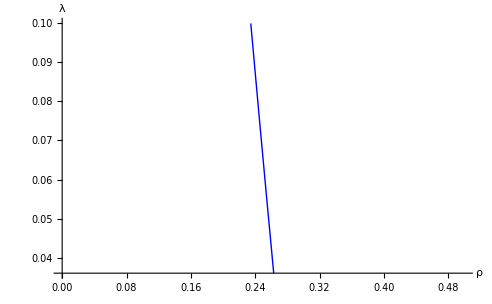

```mathematica
lamtr=Plot[(-(π ρ1-π ρ ρ1+Nd Ld ρ Log[ρ])/((-1+ρ) (Nd Ld-π ρ1))/.Ld->0.58/2/.ρ1->4.111),{ρ,0,0.5},PlotRange->{0.036,0.1},AxesLabel->{"ρ","λ"},LabelStyle->Directive[25], PlotStyle->{Blue, Thick}]
```

```mathematica
FindMaximum[i,{ρ,0.05}]
```

{8.3514,{ρ→0.271438}}

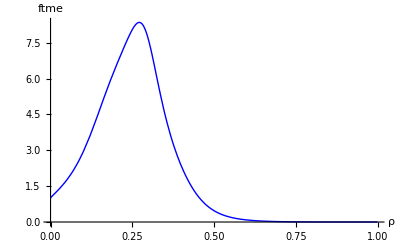

```mathematica
Plot[(i),{ρ,0,1},PlotRange->All,AxesLabel->{"ρ","ftme"},LabelStyle->Directive[25], PlotStyle->{Blue, Thick}]
```

```mathematica
(-(π ρ1-π ρ ρ1+Nd Ld ρ Log[ρ])/((-1+ρ) (Nd Ld-π ρ1))/.Ld->0.58/2/.ρ1->4.111)/.ρ->0.27144
```

0.0178033

```mathematica
58
```

58

```mathematica
i/.ρ->0.1
```

13.1505

```mathematica
(2 L1 (λ (-1+ρ)+ρ Log[ρ]))/(λ (-1+ρ) ρ1)/.L1->Ld/(1+1/λ)/.Ld->0.75/.ρ1->5.4/.λ->0.1/.ρ->0.046
```

0.0627446

```mathematica
%*100/(2π)
```

0.999984

```mathematica
Solve[(-(π ρ1-π ρ ρ1+100 Ld ρ Log[ρ])/((-1+ρ) (100 Ld-π ρ1))/.Ld->0.3/.ρ1->5.4)==0,ρ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ρ→0.350209},{ρ→1.}}

```mathematica
(-(π ρ1-π ρ ρ1+100 Ld ρ Log[ρ])/((-1+ρ) (100 Ld-π ρ1))/.Ld->0.3/.ρ1->5.4)/.ρ->0.3405893719364189
```

0.0211037

auti edw einai i max fr gia to CLIC

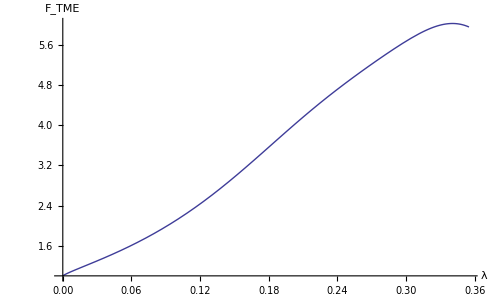

```mathematica
ftme=Plot[i,{ρ,0,0.355},PlotRange->Automatic,AxesLabel->{"λ","F_TME"},LabelStyle->Directive[20]]
```

```mathematica
FindMaximum[i,{ρ,0.34}]
```

{6.02302,{ρ→0.340589}}

```mathematica
p6=Graphics[{PointSize[Large],Blue,Point[{0.3405893719364189,6.023017965425712}]}]
```

-Graphics-

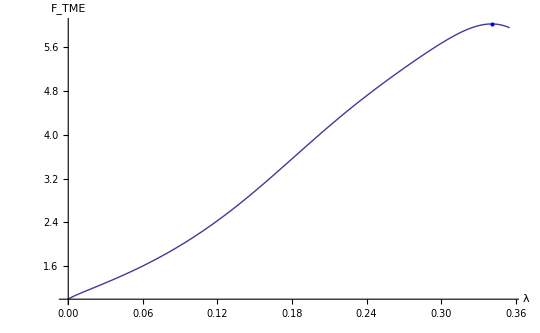

```mathematica
Show[ftme,p6,PlotRange->Automatic]
```

```mathematica
e=FullSimplify[e/.r->1/ρ,{λ>0,ρ>0,ρ1>0,ρ<1,L1>0,er>0}]
```

1/(120 λ^4 (1-ρ)^5 (1+ρ) ρ1^3 β_0)C (3 L1^4 (20 λ^2 (-1+ρ)^4 ρ^3-40 λ (-1+ρ)^3 ρ^4+10 λ^3 (-1+ρ)^4 ρ^2 (1+ρ)-10 (-1+ρ) ρ^5 (-11+5 ρ)-λ^4 (-1+ρ)^5 (2+5 ρ (1+ρ))-20 ρ^4 Log[ρ] (λ^3 (-1+ρ)^3-4 λ (-1+ρ)^2 ρ+ρ (2+(4-3 ρ) ρ)+ρ (λ (-1+ρ)+ρ)^2 Log[ρ]))-10 λ^2 (-1+ρ)^2 (L1^2 (-6 λ (-1+ρ)^2 ρ^2 (1+ρ)+3 ρ^3 (-1+ρ^2)+2 λ^2 (-1+ρ)^3 (2+3 ρ (1+ρ))+6 ρ^4 Log[ρ] (2 λ (-1+ρ)-ρ+ρ Log[ρ])) β_0^2+2 ρ1 η_0 (L1^2 ((-1+ρ) (3 ρ^3 (-1+3 ρ)+3 λ ρ^2 (-1+ρ^2)-λ^2 (-1+ρ)^2 (2+3 ρ (1+ρ)))-6 ρ^4 (λ (-1+ρ)+ρ) Log[ρ])+3 λ^2 (-1+ρ)^3 (2+ρ+ρ^2) ρ1 η_0)))

```mathematica
emi
```

(C L1^3 (-6 λ (-1+ρ)^2 ρ^2 (1+ρ)+3 ρ^3 (-1+ρ^2)+2 λ^2 (-1+ρ)^3 (2+3 ρ (1+ρ))+6 ρ^4 Log[1/ρ] (-2 λ (-1+ρ)+ρ+ρ Log[1/ρ])))/(6 √30 λ^3 (-1+ρ)^3 (1+ρ) ρ1^3 √(((-1+ρ)^3 (2+ρ+ρ^2) (-6 λ (-1+ρ)^2 ρ^2 (1+ρ)+3 ρ^3 (-1+ρ^2)+2 λ^2 (-1+ρ)^3 (2+3 ρ (1+ρ))+6 ρ^4 Log[1/ρ] (-2 λ (-1+ρ)+ρ+ρ Log[1/ρ])))/((-1+ρ)^2 (-120 λ^3 (-1+ρ)^3 ρ^2 (1+ρ)+16 λ^4 (-1+ρ)^4 (1+3 ρ (1+ρ))+15 λ^2 (-1+ρ)^2 ρ^3 (20+3 (-1+ρ) ρ (3+ρ))+45 ρ^5 (-44+ρ (-3+(-6+ρ) ρ))+90 λ (-1+ρ) ρ^4 (-8+ρ (5+(-2+ρ) ρ)))+60 ρ^4 Log[1/ρ] (-2 (-1+ρ) (2 λ^3 (-1+ρ)^3-6 λ (-2+ρ) (-1+ρ) ρ-λ^2 (-1+ρ)^2 ρ+3 ρ (2+5 ρ))+3 (-2+ρ) ρ (λ (-1+ρ)+ρ)^2 Log[1/ρ]))))

```mathematica
{β01,β02}=Simplify[Solve[emi er==e,Subscript[β, 0]],{λ>0,ρ>0,ρ1>0,ρ<1,L1>0,er>0}]
```

{{β_0→(-4 er L1^2 λ^2+6 er L1^2 λ^2 ρ-6 er L1^2 λ ρ^2-3 er L1^2 ρ^3+6 er L1^2 λ ρ^3+4 er L1^2 λ^2 ρ^3+6 er L1^2 λ ρ^4-12 er L1^2 λ^2 ρ^4+3 er L1^2 ρ^5-6 er L1^2 λ ρ^5+6 er L1^2 λ^2 ρ^5-12 er L1^2 λ ρ^4 Log[ρ]-6 er L1^2 ρ^5 Log[ρ]+12 er L1^2 λ ρ^5 Log[ρ]+6 er L1^2 ρ^5 Log[ρ]^2-Abs[(-1+ρ) (3 ρ^3 (1+ρ)-6 λ ρ^2 (-1+ρ^2)+2 λ^2 (-1+ρ)^2 (2+3 ρ+3 ρ^2))+6 (2 λ (-1+ρ)-ρ) ρ^4 Log[ρ]+6 ρ^5 Log[ρ]^2] √(-(L1^4 (-(-1+ρ)^2 (30 λ^3 (-1+ρ)^3 ρ^2 (1+ρ) (-4 er^2+3 (2+ρ+ρ^2))+45 ρ^5 (2 (22+ρ+6 ρ^2-5 ρ^3)+er^2 (-44-3 ρ-6 ρ^2+ρ^3))+90 λ (-1+ρ) ρ^4 (-4 (-2+ρ+ρ^3)+er^2 (-8+5 ρ-2 ρ^2+ρ^3))+15 λ^2 (-1+ρ)^2 ρ^3 (12 (-2+ρ+ρ^3)+er^2 (20-9 ρ+6 ρ^2+3 ρ^3))-λ^4 (-1+ρ)^4 (-16 er^2 (1+3 ρ+3 ρ^2)+9 (4+12 ρ+17 ρ^2+10 ρ^3+5 ρ^4)))+60 (-1+ρ) ρ^4 (2 er^2 λ^2 (-1+ρ)^2 ρ-12 λ (-1+ρ) ρ (-2-er^2 (-2+ρ)+ρ+ρ^3)+3 ρ (4+10 ρ+ρ^3-3 ρ^4-2 er^2 (2+5 ρ))+λ^3 (-1+ρ)^3 (-4 er^2+3 (2+ρ+ρ^2))) Log[ρ]+180 ρ^5 (λ (-1+ρ)+ρ)^2 (-2-er^2 (-2+ρ)+ρ+ρ^3) Log[ρ]^2)-60 L1^2 λ^2 (-1+ρ)^3 (2+ρ+ρ^2) ρ1 ((-1+ρ) (3 (1-3 ρ) ρ^3-3 λ ρ^2 (-1+ρ^2)+λ^2 (-1+ρ)^2 (2+3 ρ+3 ρ^2))+6 ρ^4 (λ (-1+ρ)+ρ) Log[ρ]) η_0+180 λ^4 (-1+ρ)^6 (2+ρ+ρ^2)^2 ρ1^2 η_0^2)/((-1+ρ)^2 (-120 λ^3 (-1+ρ)^3 ρ^2 (1+ρ)+16 λ^4 (-1+ρ)^4 (1+3 ρ+3 ρ^2)+45 ρ^5 (-44-3 ρ-6 ρ^2+ρ^3)+15 λ^2 (-1+ρ)^2 ρ^3 (20-9 ρ+6 ρ^2+3 ρ^3)+90 λ ρ^4 (8-13 ρ+7 ρ^2-3 ρ^3+ρ^4))+120 (-1+ρ) ρ^4 (2 λ^3 (-1+ρ)^3-λ^2 (-1+ρ)^2 ρ+3 ρ (2+5 ρ)-6 λ ρ (2-3 ρ+ρ^2)) Log[ρ]+180 (-2+ρ) ρ^5 (λ (-1+ρ)+ρ)^2 Log[ρ]^2)))/(√30 L1 λ ((-1+ρ) (3 ρ^3 (1+ρ)-6 λ ρ^2 (-1+ρ^2)+2 λ^2 (-1+ρ)^2 (2+3 ρ+3 ρ^2))+6 (2 λ (-1+ρ)-ρ) ρ^4 Log[ρ]+6 ρ^5 Log[ρ]^2) √(((-1+ρ)^3 (2+ρ+ρ^2) (-6 λ (-1+ρ)^2 ρ^2 (1+ρ)+3 ρ^3 (-1+ρ^2)+2 λ^2 (-1+ρ)^3 (2+3 ρ (1+ρ))+6 ρ^4 Log[ρ] (2 λ (-1+ρ)-ρ+ρ Log[ρ])))/((-1+ρ)^2 (-120 λ^3 (-1+ρ)^3 ρ^2 (1+ρ)+16 λ^4 (-1+ρ)^4 (1+3 ρ (1+ρ))+15 λ^2 (-1+ρ)^2 ρ^3 (20+3 (-1+ρ) ρ (3+ρ))+45 ρ^5 (-44+ρ (-3+(-6+ρ) ρ))+90 λ (-1+ρ) ρ^4 (-8+ρ (5+(-2+ρ) ρ)))-60 ρ^4 Log[ρ] (-2 (-1+ρ) (2 λ^3 (-1+ρ)^3-6 λ (-2+ρ) (-1+ρ) ρ-λ^2 (-1+ρ)^2 ρ+3 ρ (2+5 ρ))-3 (-2+ρ) ρ (λ (-1+ρ)+ρ)^2 Log[ρ]))))},{β_0→(-4 er L1^2 λ^2+6 er L1^2 λ^2 ρ-6 er L1^2 λ ρ^2-3 er L1^2 ρ^3+6 er L1^2 λ ρ^3+4 er L1^2 λ^2 ρ^3+6 er L1^2 λ ρ^4-12 er L1^2 λ^2 ρ^4+3 er L1^2 ρ^5-6 er L1^2 λ ρ^5+6 er L1^2 λ^2 ρ^5-12 er L1^2 λ ρ^4 Log[ρ]-6 er L1^2 ρ^5 Log[ρ]+12 er L1^2 λ ρ^5 Log[ρ]+6 er L1^2 ρ^5 Log[ρ]^2+Abs[(-1+ρ) (3 ρ^3 (1+ρ)-6 λ ρ^2 (-1+ρ^2)+2 λ^2 (-1+ρ)^2 (2+3 ρ+3 ρ^2))+6 (2 λ (-1+ρ)-ρ) ρ^4 Log[ρ]+6 ρ^5 Log[ρ]^2] √(-(L1^4 (-(-1+ρ)^2 (30 λ^3 (-1+ρ)^3 ρ^2 (1+ρ) (-4 er^2+3 (2+ρ+ρ^2))+45 ρ^5 (2 (22+ρ+6 ρ^2-5 ρ^3)+er^2 (-44-3 ρ-6 ρ^2+ρ^3))+90 λ (-1+ρ) ρ^4 (-4 (-2+ρ+ρ^3)+er^2 (-8+5 ρ-2 ρ^2+ρ^3))+15 λ^2 (-1+ρ)^2 ρ^3 (12 (-2+ρ+ρ^3)+er^2 (20-9 ρ+6 ρ^2+3 ρ^3))-λ^4 (-1+ρ)^4 (-16 er^2 (1+3 ρ+3 ρ^2)+9 (4+12 ρ+17 ρ^2+10 ρ^3+5 ρ^4)))+60 (-1+ρ) ρ^4 (2 er^2 λ^2 (-1+ρ)^2 ρ-12 λ (-1+ρ) ρ (-2-er^2 (-2+ρ)+ρ+ρ^3)+3 ρ (4+10 ρ+ρ^3-3 ρ^4-2 er^2 (2+5 ρ))+λ^3 (-1+ρ)^3 (-4 er^2+3 (2+ρ+ρ^2))) Log[ρ]+180 ρ^5 (λ (-1+ρ)+ρ)^2 (-2-er^2 (-2+ρ)+ρ+ρ^3) Log[ρ]^2)-60 L1^2 λ^2 (-1+ρ)^3 (2+ρ+ρ^2) ρ1 ((-1+ρ) (3 (1-3 ρ) ρ^3-3 λ ρ^2 (-1+ρ^2)+λ^2 (-1+ρ)^2 (2+3 ρ+3 ρ^2))+6 ρ^4 (λ (-1+ρ)+ρ) Log[ρ]) η_0+180 λ^4 (-1+ρ)^6 (2+ρ+ρ^2)^2 ρ1^2 η_0^2)/((-1+ρ)^2 (-120 λ^3 (-1+ρ)^3 ρ^2 (1+ρ)+16 λ^4 (-1+ρ)^4 (1+3 ρ+3 ρ^2)+45 ρ^5 (-44-3 ρ-6 ρ^2+ρ^3)+15 λ^2 (-1+ρ)^2 ρ^3 (20-9 ρ+6 ρ^2+3 ρ^3)+90 λ ρ^4 (8-13 ρ+7 ρ^2-3 ρ^3+ρ^4))+120 (-1+ρ) ρ^4 (2 λ^3 (-1+ρ)^3-λ^2 (-1+ρ)^2 ρ+3 ρ (2+5 ρ)-6 λ ρ (2-3 ρ+ρ^2)) Log[ρ]+180 (-2+ρ) ρ^5 (λ (-1+ρ)+ρ)^2 Log[ρ]^2)))/(√30 L1 λ ((-1+ρ) (3 ρ^3 (1+ρ)-6 λ ρ^2 (-1+ρ^2)+2 λ^2 (-1+ρ)^2 (2+3 ρ+3 ρ^2))+6 (2 λ (-1+ρ)-ρ) ρ^4 Log[ρ]+6 ρ^5 Log[ρ]^2) √(((-1+ρ)^3 (2+ρ+ρ^2) (-6 λ (-1+ρ)^2 ρ^2 (1+ρ)+3 ρ^3 (-1+ρ^2)+2 λ^2 (-1+ρ)^3 (2+3 ρ (1+ρ))+6 ρ^4 Log[ρ] (2 λ (-1+ρ)-ρ+ρ Log[ρ])))/((-1+ρ)^2 (-120 λ^3 (-1+ρ)^3 ρ^2 (1+ρ)+16 λ^4 (-1+ρ)^4 (1+3 ρ (1+ρ))+15 λ^2 (-1+ρ)^2 ρ^3 (20+3 (-1+ρ) ρ (3+ρ))+45 ρ^5 (-44+ρ (-3+(-6+ρ) ρ))+90 λ (-1+ρ) ρ^4 (-8+ρ (5+(-2+ρ) ρ)))-60 ρ^4 Log[ρ] (-2 (-1+ρ) (2 λ^3 (-1+ρ)^3-6 λ (-2+ρ) (-1+ρ) ρ-λ^2 (-1+ρ)^2 ρ+3 ρ (2+5 ρ))-3 (-2+ρ) ρ (λ (-1+ρ)+ρ)^2 Log[ρ]))))}}

```mathematica
Simplify[(-4 er L1^2 λ^2+6 er L1^2 λ^2 ρ-6 er L1^2 λ ρ^2-3 er L1^2 ρ^3+6 er L1^2 λ ρ^3+4 er L1^2 λ^2 ρ^3+6 er L1^2 λ ρ^4-12 er L1^2 λ^2 ρ^4+3 er L1^2 ρ^5-6 er L1^2 λ ρ^5+6 er L1^2 λ^2 ρ^5-12 er L1^2 λ ρ^4 Log[ρ]-6 er L1^2 ρ^5 Log[ρ]+12 er L1^2 λ ρ^5 Log[ρ]+6 er L1^2 ρ^5 Log[ρ]^2+((-1+ρ) (3 ρ^3 (1+ρ)-6 λ ρ^2 (-1+ρ^2)+2 λ^2 (-1+ρ)^2 (2+3 ρ+3 ρ^2))+6 (2 λ (-1+ρ)-ρ) ρ^4 Log[ρ]+6 ρ^5 Log[ρ]^2) √(-(L1^4 (-(-1+ρ)^2 (30 λ^3 (-1+ρ)^3 ρ^2 (1+ρ) (-4 er^2+3 (2+ρ+ρ^2))+45 ρ^5 (2 (22+ρ+6 ρ^2-5 ρ^3)+er^2 (-44-3 ρ-6 ρ^2+ρ^3))+90 λ (-1+ρ) ρ^4 (-4 (-2+ρ+ρ^3)+er^2 (-8+5 ρ-2 ρ^2+ρ^3))+15 λ^2 (-1+ρ)^2 ρ^3 (12 (-2+ρ+ρ^3)+er^2 (20-9 ρ+6 ρ^2+3 ρ^3))-λ^4 (-1+ρ)^4 (-16 er^2 (1+3 ρ+3 ρ^2)+9 (4+12 ρ+17 ρ^2+10 ρ^3+5 ρ^4)))+60 (-1+ρ) ρ^4 (2 er^2 λ^2 (-1+ρ)^2 ρ-12 λ (-1+ρ) ρ (-2-er^2 (-2+ρ)+ρ+ρ^3)+3 ρ (4+10 ρ+ρ^3-3 ρ^4-2 er^2 (2+5 ρ))+λ^3 (-1+ρ)^3 (-4 er^2+3 (2+ρ+ρ^2))) Log[ρ]+180 ρ^5 (λ (-1+ρ)+ρ)^2 (-2-er^2 (-2+ρ)+ρ+ρ^3) Log[ρ]^2)-60 L1^2 λ^2 (-1+ρ)^3 (2+ρ+ρ^2) ρ1 ((-1+ρ) (3 (1-3 ρ) ρ^3-3 λ ρ^2 (-1+ρ^2)+λ^2 (-1+ρ)^2 (2+3 ρ+3 ρ^2))+6 ρ^4 (λ (-1+ρ)+ρ) Log[ρ]) Subscript[η, 0]+180 λ^4 (-1+ρ)^6 (2+ρ+ρ^2)^2 ρ1^2 Subscript[η, 0]^2)/((-1+ρ)^2 (-120 λ^3 (-1+ρ)^3 ρ^2 (1+ρ)+16 λ^4 (-1+ρ)^4 (1+3 ρ+3 ρ^2)+45 ρ^5 (-44-3 ρ-6 ρ^2+ρ^3)+15 λ^2 (-1+ρ)^2 ρ^3 (20-9 ρ+6 ρ^2+3 ρ^3)+90 λ ρ^4 (8-13 ρ+7 ρ^2-3 ρ^3+ρ^4))+120 (-1+ρ) ρ^4 (2 λ^3 (-1+ρ)^3-λ^2 (-1+ρ)^2 ρ+3 ρ (2+5 ρ)-6 λ ρ (2-3 ρ+ρ^2)) Log[ρ]+180 (-2+ρ) ρ^5 (λ (-1+ρ)+ρ)^2 Log[ρ]^2)))/(√30 L1 λ ((-1+ρ) (3 ρ^3 (1+ρ)-6 λ ρ^2 (-1+ρ^2)+2 λ^2 (-1+ρ)^2 (2+3 ρ+3 ρ^2))+6 (2 λ (-1+ρ)-ρ) ρ^4 Log[ρ]+6 ρ^5 Log[ρ]^2) √(((-1+ρ)^3 (2+ρ+ρ^2) (-6 λ (-1+ρ)^2 ρ^2 (1+ρ)+3 ρ^3 (-1+ρ^2)+2 λ^2 (-1+ρ)^3 (2+3 ρ (1+ρ))+6 ρ^4 Log[ρ] (2 λ (-1+ρ)-ρ+ρ Log[ρ])))/((-1+ρ)^2 (-120 λ^3 (-1+ρ)^3 ρ^2 (1+ρ)+16 λ^4 (-1+ρ)^4 (1+3 ρ (1+ρ))+15 λ^2 (-1+ρ)^2 ρ^3 (20+3 (-1+ρ) ρ (3+ρ))+45 ρ^5 (-44+ρ (-3+(-6+ρ) ρ))+90 λ (-1+ρ) ρ^4 (-8+ρ (5+(-2+ρ) ρ)))-60 ρ^4 Log[ρ] (-2 (-1+ρ) (2 λ^3 (-1+ρ)^3-6 λ (-2+ρ) (-1+ρ) ρ-λ^2 (-1+ρ)^2 ρ+3 ρ (2+5 ρ))-3 (-2+ρ) ρ (λ (-1+ρ)+ρ)^2 Log[ρ]))))]
```

(er L1^2+√((-L1^4 (-(-1+ρ)^2 (30 λ^3 (-1+ρ)^3 ρ^2 (1+ρ) (-4 er^2+3 (2+ρ+ρ^2))+45 ρ^5 (2 (22+ρ+6 ρ^2-5 ρ^3)+er^2 (-44-3 ρ-6 ρ^2+ρ^3))+90 λ (-1+ρ) ρ^4 (-4 (-2+ρ+ρ^3)+er^2 (-8+5 ρ-2 ρ^2+ρ^3))+15 λ^2 (-1+ρ)^2 ρ^3 (12 (-2+ρ+ρ^3)+er^2 (20-9 ρ+6 ρ^2+3 ρ^3))-λ^4 (-1+ρ)^4 (-16 er^2 (1+3 ρ+3 ρ^2)+9 (4+12 ρ+17 ρ^2+10 ρ^3+5 ρ^4)))+60 (-1+ρ) ρ^4 (2 er^2 λ^2 (-1+ρ)^2 ρ-12 λ (-1+ρ) ρ (-2-er^2 (-2+ρ)+ρ+ρ^3)+3 ρ (4+10 ρ+ρ^3-3 ρ^4-2 er^2 (2+5 ρ))+λ^3 (-1+ρ)^3 (-4 er^2+3 (2+ρ+ρ^2))) Log[ρ]+180 ρ^5 (λ (-1+ρ)+ρ)^2 (-2-er^2 (-2+ρ)+ρ+ρ^3) Log[ρ]^2)+60 L1^2 λ^2 (-1+ρ)^3 (2+ρ+ρ^2) ρ1 ((-1+ρ) (3 (1-3 ρ) ρ^3-3 λ ρ^2 (-1+ρ^2)+λ^2 (-1+ρ)^2 (2+3 ρ+3 ρ^2))+6 ρ^4 (λ (-1+ρ)+ρ) Log[ρ]) η_0-180 λ^4 (-1+ρ)^6 (2+ρ+ρ^2)^2 ρ1^2 η_0^2)/((-1+ρ)^2 (-120 λ^3 (-1+ρ)^3 ρ^2 (1+ρ)+16 λ^4 (-1+ρ)^4 (1+3 ρ+3 ρ^2)+45 ρ^5 (-44-3 ρ-6 ρ^2+ρ^3)+15 λ^2 (-1+ρ)^2 ρ^3 (20-9 ρ+6 ρ^2+3 ρ^3)+90 λ ρ^4 (8-13 ρ+7 ρ^2-3 ρ^3+ρ^4))+120 (-1+ρ) ρ^4 (2 λ^3 (-1+ρ)^3-λ^2 (-1+ρ)^2 ρ+3 ρ (2+5 ρ)-6 λ ρ (2-3 ρ+ρ^2)) Log[ρ]+180 (-2+ρ) ρ^5 (λ (-1+ρ)+ρ)^2 Log[ρ]^2)))/(√30 L1 λ √(((-1+ρ)^3 (2+ρ+ρ^2) (-6 λ (-1+ρ)^2 ρ^2 (1+ρ)+3 ρ^3 (-1+ρ^2)+2 λ^2 (-1+ρ)^3 (2+3 ρ (1+ρ))+6 ρ^4 Log[ρ] (2 λ (-1+ρ)-ρ+ρ Log[ρ])))/((-1+ρ)^2 (-120 λ^3 (-1+ρ)^3 ρ^2 (1+ρ)+16 λ^4 (-1+ρ)^4 (1+3 ρ (1+ρ))+15 λ^2 (-1+ρ)^2 ρ^3 (20+3 (-1+ρ) ρ (3+ρ))+45 ρ^5 (-44+ρ (-3+(-6+ρ) ρ))+90 λ (-1+ρ) ρ^4 (-8+ρ (5+(-2+ρ) ρ)))-60 ρ^4 Log[ρ] (-2 (-1+ρ) (2 λ^3 (-1+ρ)^3-6 λ (-2+ρ) (-1+ρ) ρ-λ^2 (-1+ρ)^2 ρ+3 ρ (2+5 ρ))-3 (-2+ρ) ρ (λ (-1+ρ)+ρ)^2 Log[ρ]))))

```mathematica
FullSimplify[(-4 er L1^2 λ^2+6 er L1^2 λ^2 ρ-6 er L1^2 λ ρ^2-3 er L1^2 ρ^3+6 er L1^2 λ ρ^3+4 er L1^2 λ^2 ρ^3+6 er L1^2 λ ρ^4-12 er L1^2 λ^2 ρ^4+3 er L1^2 ρ^5-6 er L1^2 λ ρ^5+6 er L1^2 λ^2 ρ^5-12 er L1^2 λ ρ^4 Log[ρ]-6 er L1^2 ρ^5 Log[ρ]+12 er L1^2 λ ρ^5 Log[ρ]+6 er L1^2 ρ^5 Log[ρ]^2)/((√30 L1 λ ((-1+ρ) (3 ρ^3 (1+ρ)-6 λ ρ^2 (-1+ρ^2)+2 λ^2 (-1+ρ)^2 (2+3 ρ+3 ρ^2))+6 (2 λ (-1+ρ)-ρ) ρ^4 Log[ρ]+6 ρ^5 Log[ρ]^2) √(((-1+ρ)^3 (2+ρ+ρ^2) (-6 λ (-1+ρ)^2 ρ^2 (1+ρ)+3 ρ^3 (-1+ρ^2)+2 λ^2 (-1+ρ)^3 (2+3 ρ (1+ρ))+6 ρ^4 Log[ρ] (2 λ (-1+ρ)-ρ+ρ Log[ρ])))/((-1+ρ)^2 (-120 λ^3 (-1+ρ)^3 ρ^2 (1+ρ)+16 λ^4 (-1+ρ)^4 (1+3 ρ (1+ρ))+15 λ^2 (-1+ρ)^2 ρ^3 (20+3 (-1+ρ) ρ (3+ρ))+45 ρ^5 (-44+ρ (-3+(-6+ρ) ρ))+90 λ (-1+ρ) ρ^4 (-8+ρ (5+(-2+ρ) ρ)))-60 ρ^4 Log[ρ] (-2 (-1+ρ) (2 λ^3 (-1+ρ)^3-6 λ (-2+ρ) (-1+ρ) ρ-λ^2 (-1+ρ)^2 ρ+3 ρ (2+5 ρ))-3 (-2+ρ) ρ (λ (-1+ρ)+ρ)^2 Log[ρ])))))/.er->1]
```

L1/(√30 λ √(((-1+ρ)^3 (2+ρ+ρ^2) (-6 λ (-1+ρ)^2 ρ^2 (1+ρ)+3 ρ^3 (-1+ρ^2)+2 λ^2 (-1+ρ)^3 (2+3 ρ (1+ρ))+6 ρ^4 Log[ρ] (2 λ (-1+ρ)-ρ+ρ Log[ρ])))/((-1+ρ)^2 (-120 λ^3 (-1+ρ)^3 ρ^2 (1+ρ)+16 λ^4 (-1+ρ)^4 (1+3 ρ (1+ρ))+15 λ^2 (-1+ρ)^2 ρ^3 (20+3 (-1+ρ) ρ (3+ρ))+45 ρ^5 (-44+ρ (-3+(-6+ρ) ρ))+90 λ (-1+ρ) ρ^4 (-8+ρ (5+(-2+ρ) ρ)))+60 ρ^4 Log[ρ] (2 (-1+ρ) (2 λ^3 (-1+ρ)^3-6 λ (-2+ρ) (-1+ρ) ρ-λ^2 (-1+ρ)^2 ρ+3 ρ (2+5 ρ))+3 (-2+ρ) ρ (λ (-1+ρ)+ρ)^2 Log[ρ]))))

```mathematica
FullSimplify[Solve[((-1+ρ) (3 ρ^3 (1+ρ)-6 λ ρ^2 (-1+ρ^2)+2 λ^2 (-1+ρ)^2 (2+3 ρ+3 ρ^2))+6 (2 λ (-1+ρ)-ρ) ρ^4 Log[ρ]+6 ρ^5 Log[ρ]^2) √(-(L1^4 (-(-1+ρ)^2 (30 λ^3 (-1+ρ)^3 ρ^2 (1+ρ) (-4 er^2+3 (2+ρ+ρ^2))+45 ρ^5 (2 (22+ρ+6 ρ^2-5 ρ^3)+er^2 (-44-3 ρ-6 ρ^2+ρ^3))+90 λ (-1+ρ) ρ^4 (-4 (-2+ρ+ρ^3)+er^2 (-8+5 ρ-2 ρ^2+ρ^3))+15 λ^2 (-1+ρ)^2 ρ^3 (12 (-2+ρ+ρ^3)+er^2 (20-9 ρ+6 ρ^2+3 ρ^3))-λ^4 (-1+ρ)^4 (-16 er^2 (1+3 ρ+3 ρ^2)+9 (4+12 ρ+17 ρ^2+10 ρ^3+5 ρ^4)))+60 (-1+ρ) ρ^4 (2 er^2 λ^2 (-1+ρ)^2 ρ-12 λ (-1+ρ) ρ (-2-er^2 (-2+ρ)+ρ+ρ^3)+3 ρ (4+10 ρ+ρ^3-3 ρ^4-2 er^2 (2+5 ρ))+λ^3 (-1+ρ)^3 (-4 er^2+3 (2+ρ+ρ^2))) Log[ρ]+180 ρ^5 (λ (-1+ρ)+ρ)^2 (-2-er^2 (-2+ρ)+ρ+ρ^3) Log[ρ]^2)-60 L1^2 λ^2 (-1+ρ)^3 (2+ρ+ρ^2) ρ1 ((-1+ρ) (3 (1-3 ρ) ρ^3-3 λ ρ^2 (-1+ρ^2)+λ^2 (-1+ρ)^2 (2+3 ρ+3 ρ^2))+6 ρ^4 (λ (-1+ρ)+ρ) Log[ρ]) Subscript[η, 0]+180 λ^4 (-1+ρ)^6 (2+ρ+ρ^2)^2 ρ1^2 Subscript[η, 0]^2)/((-1+ρ)^2 (-120 λ^3 (-1+ρ)^3 ρ^2 (1+ρ)+16 λ^4 (-1+ρ)^4 (1+3 ρ+3 ρ^2)+45 ρ^5 (-44-3 ρ-6 ρ^2+ρ^3)+15 λ^2 (-1+ρ)^2 ρ^3 (20-9 ρ+6 ρ^2+3 ρ^3)+90 λ ρ^4 (8-13 ρ+7 ρ^2-3 ρ^3+ρ^4))+120 (-1+ρ) ρ^4 (2 λ^3 (-1+ρ)^3-λ^2 (-1+ρ)^2 ρ+3 ρ (2+5 ρ)-6 λ ρ (2-3 ρ+ρ^2)) Log[ρ]+180 (-2+ρ) ρ^5 (λ (-1+ρ)+ρ)^2 Log[ρ]^2))==0,Subscript[η, 0] ]]
```

{{η_0→1/(30 λ^4 (-1+ρ)^6 (2+ρ+ρ^2)^2 ρ1^2)(20 L1^2 λ^4 ρ1-80 L1^2 λ^4 ρ ρ1+30 L1^2 λ^3 ρ^2 ρ1+115 L1^2 λ^4 ρ^2 ρ1+30 L1^2 λ^2 ρ^3 ρ1-105 L1^2 λ^3 ρ^3 ρ1-100 L1^2 λ^4 ρ^3 ρ1-195 L1^2 λ^2 ρ^4 ρ1+105 L1^2 λ^3 ρ^4 ρ1+160 L1^2 λ^4 ρ^4 ρ1+450 L1^2 λ^2 ρ^5 ρ1+15 L1^2 λ^3 ρ^5 ρ1-260 L1^2 λ^4 ρ^5 ρ1-495 L1^2 λ^2 ρ^6 ρ1-75 L1^2 λ^3 ρ^6 ρ1+230 L1^2 λ^4 ρ^6 ρ1+330 L1^2 λ^2 ρ^7 ρ1+45 L1^2 λ^3 ρ^7 ρ1-140 L1^2 λ^4 ρ^7 ρ1-225 L1^2 λ^2 ρ^8 ρ1-45 L1^2 λ^3 ρ^8 ρ1+100 L1^2 λ^4 ρ^8 ρ1+150 L1^2 λ^2 ρ^9 ρ1+45 L1^2 λ^3 ρ^9 ρ1-60 L1^2 λ^4 ρ^9 ρ1-45 L1^2 λ^2 ρ^10 ρ1-15 L1^2 λ^3 ρ^10 ρ1+15 L1^2 λ^4 ρ^10 ρ1+30 L1^2 λ^2 (-1+ρ)^3 ρ^4 (λ (-1+ρ)+ρ) (2+ρ+ρ^2) ρ1 Log[ρ]-√5 √((-1+er^2) L1^4 λ^4 (-1+ρ)^6 (2+ρ+ρ^2)^2 ρ1^2 ((-1+ρ)^2 (-120 λ^3 (-1+ρ)^3 ρ^2 (1+ρ)+16 λ^4 (-1+ρ)^4 (1+3 ρ+3 ρ^2)+45 ρ^5 (-44-3 ρ-6 ρ^2+ρ^3)+15 λ^2 (-1+ρ)^2 ρ^3 (20-9 ρ+6 ρ^2+3 ρ^3)+90 λ ρ^4 (8-13 ρ+7 ρ^2-3 ρ^3+ρ^4))+120 (-1+ρ) ρ^4 (2 λ^3 (-1+ρ)^3-λ^2 (-1+ρ)^2 ρ+3 ρ (2+5 ρ)-6 λ ρ (2-3 ρ+ρ^2)) Log[ρ]+180 (-2+ρ) ρ^5 (λ (-1+ρ)+ρ)^2 Log[ρ]^2)))},{η_0→1/(30 λ^4 (-1+ρ)^6 (2+ρ+ρ^2)^2 ρ1^2)(20 L1^2 λ^4 ρ1-80 L1^2 λ^4 ρ ρ1+30 L1^2 λ^3 ρ^2 ρ1+115 L1^2 λ^4 ρ^2 ρ1+30 L1^2 λ^2 ρ^3 ρ1-105 L1^2 λ^3 ρ^3 ρ1-100 L1^2 λ^4 ρ^3 ρ1-195 L1^2 λ^2 ρ^4 ρ1+105 L1^2 λ^3 ρ^4 ρ1+160 L1^2 λ^4 ρ^4 ρ1+450 L1^2 λ^2 ρ^5 ρ1+15 L1^2 λ^3 ρ^5 ρ1-260 L1^2 λ^4 ρ^5 ρ1-495 L1^2 λ^2 ρ^6 ρ1-75 L1^2 λ^3 ρ^6 ρ1+230 L1^2 λ^4 ρ^6 ρ1+330 L1^2 λ^2 ρ^7 ρ1+45 L1^2 λ^3 ρ^7 ρ1-140 L1^2 λ^4 ρ^7 ρ1-225 L1^2 λ^2 ρ^8 ρ1-45 L1^2 λ^3 ρ^8 ρ1+100 L1^2 λ^4 ρ^8 ρ1+150 L1^2 λ^2 ρ^9 ρ1+45 L1^2 λ^3 ρ^9 ρ1-60 L1^2 λ^4 ρ^9 ρ1-45 L1^2 λ^2 ρ^10 ρ1-15 L1^2 λ^3 ρ^10 ρ1+15 L1^2 λ^4 ρ^10 ρ1+30 L1^2 λ^2 (-1+ρ)^3 ρ^4 (λ (-1+ρ)+ρ) (2+ρ+ρ^2) ρ1 Log[ρ]+√5 √((-1+er^2) L1^4 λ^4 (-1+ρ)^6 (2+ρ+ρ^2)^2 ρ1^2 ((-1+ρ)^2 (-120 λ^3 (-1+ρ)^3 ρ^2 (1+ρ)+16 λ^4 (-1+ρ)^4 (1+3 ρ+3 ρ^2)+45 ρ^5 (-44-3 ρ-6 ρ^2+ρ^3)+15 λ^2 (-1+ρ)^2 ρ^3 (20-9 ρ+6 ρ^2+3 ρ^3)+90 λ ρ^4 (8-13 ρ+7 ρ^2-3 ρ^3+ρ^4))+120 (-1+ρ) ρ^4 (2 λ^3 (-1+ρ)^3-λ^2 (-1+ρ)^2 ρ+3 ρ (2+5 ρ)-6 λ ρ (2-3 ρ+ρ^2)) Log[ρ]+180 (-2+ρ) ρ^5 (λ (-1+ρ)+ρ)^2 Log[ρ]^2)))}}

```mathematica
FullSimplify[1/(30 λ^4 (-1+ρ)^6 (2+ρ+ρ^2)^2 ρ1^2)(20 L1^2 λ^4 ρ1-80 L1^2 λ^4 ρ ρ1+30 L1^2 λ^3 ρ^2 ρ1+115 L1^2 λ^4 ρ^2 ρ1+30 L1^2 λ^2 ρ^3 ρ1-105 L1^2 λ^3 ρ^3 ρ1-100 L1^2 λ^4 ρ^3 ρ1-195 L1^2 λ^2 ρ^4 ρ1+105 L1^2 λ^3 ρ^4 ρ1+160 L1^2 λ^4 ρ^4 ρ1+450 L1^2 λ^2 ρ^5 ρ1+15 L1^2 λ^3 ρ^5 ρ1-260 L1^2 λ^4 ρ^5 ρ1-495 L1^2 λ^2 ρ^6 ρ1-75 L1^2 λ^3 ρ^6 ρ1+230 L1^2 λ^4 ρ^6 ρ1+330 L1^2 λ^2 ρ^7 ρ1+45 L1^2 λ^3 ρ^7 ρ1-140 L1^2 λ^4 ρ^7 ρ1-225 L1^2 λ^2 ρ^8 ρ1-45 L1^2 λ^3 ρ^8 ρ1+100 L1^2 λ^4 ρ^8 ρ1+150 L1^2 λ^2 ρ^9 ρ1+45 L1^2 λ^3 ρ^9 ρ1-60 L1^2 λ^4 ρ^9 ρ1-45 L1^2 λ^2 ρ^10 ρ1-15 L1^2 λ^3 ρ^10 ρ1+15 L1^2 λ^4 ρ^10 ρ1+30 L1^2 λ^2 (-1+ρ)^3 ρ^4 (λ (-1+ρ)+ρ) (2+ρ+ρ^2) ρ1 Log[ρ]-√5 √((-1+er^2) L1^4 λ^4 (-1+ρ)^6 (2+ρ+ρ^2)^2 ρ1^2 ((-1+ρ)^2 (-120 λ^3 (-1+ρ)^3 ρ^2 (1+ρ)+16 λ^4 (-1+ρ)^4 (1+3 ρ+3 ρ^2)+45 ρ^5 (-44-3 ρ-6 ρ^2+ρ^3)+15 λ^2 (-1+ρ)^2 ρ^3 (20-9 ρ+6 ρ^2+3 ρ^3)+90 λ ρ^4 (8-13 ρ+7 ρ^2-3 ρ^3+ρ^4))+120 (-1+ρ) ρ^4 (2 λ^3 (-1+ρ)^3-λ^2 (-1+ρ)^2 ρ+3 ρ (2+5 ρ)-6 λ ρ (2-3 ρ+ρ^2)) Log[ρ]+180 (-2+ρ) ρ^5 (λ (-1+ρ)+ρ)^2 Log[ρ]^2))),{λ>0,ρ>0,ρ1>0,ρ<1,L1>0,er>0}]
```

1/(30 λ^2 (-1+ρ)^3 (2+ρ+ρ^2) ρ1)L1^2 (5 (-1+ρ) (3 (1-3 ρ) ρ^3-3 λ ρ^2 (-1+ρ^2)+λ^2 (-1+ρ)^2 (2+3 ρ (1+ρ)))+30 ρ^4 (λ (-1+ρ)+ρ) Log[ρ]+√5 √((-1+er^2) ((-1+ρ)^2 (-120 λ^3 (-1+ρ)^3 ρ^2 (1+ρ)+16 λ^4 (-1+ρ)^4 (1+3 ρ (1+ρ))+15 λ^2 (-1+ρ)^2 ρ^3 (20+3 (-1+ρ) ρ (3+ρ))+45 ρ^5 (-44+ρ (-3+(-6+ρ) ρ))+90 λ (-1+ρ) ρ^4 (-8+ρ (5+(-2+ρ) ρ)))+60 ρ^4 Log[ρ] (2 (-1+ρ) (2 λ^3 (-1+ρ)^3-6 λ (-2+ρ) (-1+ρ) ρ-λ^2 (-1+ρ)^2 ρ+3 ρ (2+5 ρ))+3 (-2+ρ) ρ (λ (-1+ρ)+ρ)^2 Log[ρ]))))

```mathematica
eta/.L1->Ld/(1+1/λ)/.Ld->0.3/.ρ->0.34/.λ->0.021103747338792337/.ρ1->5.4
```

0.000118312

```mathematica
beta/.L1->Ld/(1+1/λ)/.Ld->0.3/.ρ->0.340589/.λ->0.021103747338792337/.ρ1->5.4
```

0.0741757

```mathematica
red=Simplify[(s2 (ηmin ηr+s1 θ+θ̃))/(ηmin ηr-ηss+s1 θ+s2 θ+θ̃)/.ηss->-(2 s3 (ηmin ηr+s1 θ+θ̃))/(s2+(√(4 s3 (ηmin ηr+s1 θ) (-(Ld+s1) ηmin ηr+(Ld (Ld+s1)+βxcd^2) θ)+s2^2 (ηmin^2 ηr^2-2 Ld ηmin ηr θ+(Ld^2+βxcd^2) θ^2)+θ̃ (-8 (Ld+s1) s3 ηmin ηr+4 s3 (Ld^2-s1^2+βxcd^2) θ+2 s2^2 (ηmin ηr-Ld θ)+(s2^2-4 (Ld+s1) s3) θ̃)))/(√(ηmin^2 ηr^2-2 Ld ηmin ηr θ+(Ld^2+βxcd^2) θ^2+θ̃ (2 ηmin ηr-2 Ld θ+θ̃))))/.{ηr->1,βr->1}/.θ̃->(Ld^2 (-λ^2+ρ))/((1+λ)^2 ρ1)/.θ->(Ld (-λ+ρ))/((1+λ) ρ1)/.ηxcd->ηr ηmin/.ηmin->(L1^2 (ρ^4+3 λ ρ^4+λ^2 (1-3 ρ^3)))/(6 λ^2 (-1+ρ^3) ρ1)/.βxcd->L1/(2 √15 λ √(((-1+ρ^3) (-3 λ ρ^4+ρ^5+λ^2 (-1+3 ρ^3)))/(4 λ^4-24 λ^4 ρ^3+20 λ^2 (1+3 λ) ρ^4-3 (3+5 λ (3+4 λ)) ρ^5+(4+15 λ (1+λ)) ρ^8)))/.L1->Ld/(1+1/λ)/.Ld->0.3/.ρ1->8.5/.λ->0.25599/.ρ->1.374]
```

((0.0128928+0.0314168 s1) s2)/(0.0128928+0.0314168 s1+0.0314168 s2+((0.0000897064+0.000218593 s1) s3)/(0.00347892 s2+1. √(0.0000121029 s2^2+(-0.0000535249-0.000309267 s1-0.000435789 s1^2) s3)))

```mathematica
Reduce[red>0&&s1>0&&s2>0&&s3>0,{s1,s2,s3}]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

s1>0&&s2>0&&0<s3≤(7.09418×10^31 s2^2)/(3.13739×10^32+1.81278×10^33 s1+2.5544×10^33 s1^2)

```mathematica
(7.094184777632836*^31 s2^2)/(3.1373916802113103*^32+1.8127833737107387*^33 s1+2.5543986490168347*^33 s1^2)/.s1->0.7/.s2->0.65
```

0.0105749

integrals

```mathematica
Subscript[θ̃, 1]=∫∫(1/ρ1)ⅆsⅆs
```

s^2/(2 ρ1)

```mathematica
Subscript[θ, 1]=∫(1/ρ1)ⅆs
```

s/ρ1

```mathematica
Subscript[th, L1]=Subscript[θ, 1]/.s->L1
```

L1/ρ1

```mathematica
Subscript[tt, L1]=Subscript[θ̃, 1]/.s->L1
```

L1^2/(2 ρ1)

```mathematica
ρ2=FullSimplify[FullSimplify[(-(-Ld+L1+s-r s) ρ1)/(Ld-L1)]/.r->1/ρ/.L1->Ld/(1+1/λ)/.Ld->L/2]
```

ρ1-(2 s (1+λ) (-1+ρ) ρ1)/(L ρ)

```mathematica
Subscript[θ, 2]=Simplify[∫_L1^s (1/ρ2)ⅆs,{r>0,r>1,λ>0,ρ1>0,L1<s,L1>0,Ld>0,L1<Ld}]
```

ConditionalExpression[(Ld ρ (Log[ρ1-(L1 (1+λ) (-1+ρ) ρ1)/(Ld ρ)]-Log[ρ1-(s (1+λ) (-1+ρ) ρ1)/(Ld ρ)]))/((1+λ) (-1+ρ) ρ1),s+s λ-Ld Re[ρ/(-1+ρ)]<0||L1+L1 λ-Ld Re[ρ/(-1+ρ)]>0||ρ/(-1+ρ)∉ℝ]

```mathematica
Subscript[θ, 2]=FullSimplify[(Ld ρ (Log[ρ1-(L1 (1+λ) (-1+ρ) ρ1)/(Ld ρ)]-Log[ρ1-(s (1+λ) (-1+ρ) ρ1)/(Ld ρ)]))/((1+λ) (-1+ρ) ρ1)/.Log[ρ1-(L1 (1+λ) (-1+ρ) ρ1)/(Ld ρ)]-Log[ρ1-(s (1+λ) (-1+ρ) ρ1)/(Ld ρ)]->Log[(ρ1-(L1 (1+λ) (-1+ρ) ρ1)/(Ld ρ))/(ρ1-(s (1+λ) (-1+ρ) ρ1)/(Ld ρ))]/.L1->Ld/(1+1/λ)/.Ld->L/2]
```

(L ρ Log[(L (λ+ρ-λ ρ))/(-2 s (1+λ) (-1+ρ)+L ρ)])/(2 (1+λ) (-1+ρ) ρ1)

```mathematica
Subscript[θ̃, 2]=Simplify[∫_L1^s (Subscript[θ, 2])ⅆs,{r>0,r>1,λ>0,ρ1>0,L1>0,L1<s,Ld>0,L1<Ld,(L ρ)/(-1+ρ)∉Reals}]
```

(L ρ (-L1+s-((2 L1 (1+λ) (-1+ρ)-L ρ) Log[(L (λ+ρ-λ ρ))/(-2 L1 (1+λ) (-1+ρ)+L ρ)])/(2 (1+λ) (-1+ρ))+((2 s (1+λ) (-1+ρ)-L ρ) Log[(L (λ+ρ-λ ρ))/(-2 s (1+λ) (-1+ρ)+L ρ)])/(2 (1+λ) (-1+ρ))))/(2 (1+λ) (-1+ρ) ρ1)

```mathematica
Subscript[θ̃, 2]=FullSimplify[(L ρ (-L1+s-((2 L1 (1+λ) (-1+ρ)-L ρ) Log[(L (λ+ρ-λ ρ))/(-2 L1 (1+λ) (-1+ρ)+L ρ)])/(2 (1+λ) (-1+ρ))+((2 s (1+λ) (-1+ρ)-L ρ) Log[(L (λ+ρ-λ ρ))/(-2 s (1+λ) (-1+ρ)+L ρ)])/(2 (1+λ) (-1+ρ))))/(2 (1+λ) (-1+ρ) ρ1)/.L1->Ld/(1+1/λ)/.Ld->L/2]
```

-(L ρ ((L λ-2 s (1+λ)) (-1+ρ)+(-2 s (1+λ) (-1+ρ)+L ρ) Log[(L (λ+ρ-λ ρ))/(-2 s (1+λ) (-1+ρ)+L ρ)]))/(4 (1+λ)^2 (-1+ρ)^2 ρ1)

```mathematica
I1=∫_0^L1 Subscript[θ, 1]^2/ρ1^3 ⅆs
```

L1^3/(3 ρ1^5)

```mathematica
I2=∫_L1^(L1+L2) (Subscript[θ, 2]+Subscript[th, L1])^2/ρ2^3 ⅆs
```

$Aborted

```mathematica
I3=∫_0^L1 1/ρ1^3 ⅆs
```

L1/Abs[ρ1]^3

```mathematica
I4=∫_L1^(L1+L2) 1/ρ2^3 ⅆs
```

$Aborted

```mathematica
I5=2∫_0^L1 (-s Subscript[θ, 1]+Subscript[θ̃, 1])/ρ1^3 ⅆs
```

```mathematica
I6=2∫_L1^(L1+L2) (-s Subscript[θ, 2]+Subscript[θ̃, 2]-L1 Subscript[th, L1]+Subscript[tt, L1])/ρ2^3 ⅆs
```

```mathematica
I7=2∫_0^L1 (-s Subscript[θ, 1]+Subscript[θ̃, 1])^2/ρ1^3 ⅆs
```

```mathematica
I8=∫_L1^(L1+L2) (-s Subscript[θ, 2]+Subscript[θ̃, 2]-L1 Subscript[th, L1]+Subscript[tt, L1])^2/ρ2^3 ⅆs
```